# The reaction schema simulator

This notebook was prepared by Erik Winfree <winfree@caltech.edu> for Caltech BE/CS 191a, Winter 2022. -- still under testing --  
Do not share this with anyone who is not currently taking the class unless you have permission from Erik Winfree.

## Introduction and overview

This notebook provides stand-alone code for a reaction schema simulator with discrete stochastic semantics.  It can also be used in conjunction with David Soloveichik’s CRN simulator (http://users.ece.utexas.edu/~soloveichik/crnsimulator.html).  The code here is based on (https://www.dna.caltech.edu/ReactionSchemaSimulator/) but with some changes to avoid namespace collisions with Soloveichik’s code, specifically rxn to rxninstance and conc to count.  Also, there are some bug fixes, improvements, new examples, and there’s homework at the end.  This version will probably soon be cleaned up as v1.1 of the “official release”.  For BE/CS 191a, comments referring to papers can be ignored.  Use wisdom to examine only those examples that will be of relevance and interest to the class -- primarily just the first few (“classical CRNs”, “simple polymer systems”,  perhaps “Turing machines”, and then of course the “class lecture example of restriction enzymes” at the end. -- revise status --  

This simulator is not efficient: while it only computes new propensities for reactions involving species whose counts have changed, it still performs pattern matching against all reaction schema at every step, i.e. after every reaction event -- even if that (sometimes slow) pattern matching was performed on the same species in earlier steps.   One would like to simply memoize the pattern matching.  However, in the general case where there are many species being produced during a simulation, and they sometimes never re-occur, memoization is neither feasible nor efficient. The simulator code has many other non-optimized aspects.   (In cases where, for any given initial state, the number of reachable species is not too large, compiling to a finite CRN and using a fast SSA simulator may be possible, as will be demonstrated in a companion notebook.)  However, for basic exploration of the notion of reaction schema, with small systems with few molecules, this simulator should be enough.

Molecules with various structures are represented by Mathematica expressions.  A reaction schema is represented using standard Mathematica pattern matching semantics for the left-hand side (reactants), with matching expressions for the right-hand side (products), and a rate constant or rate formula in which the matched variables may occur.  

As examples of reaction schemas, consider:
	rxnschema[0, Poly[ ], 3.7]
	rxnschema[Poly[ ], 0, 1.0]
	rxnschema[M+Poly[x___], Poly[x,M], f[x] ]
	
The three arguments are the reactant pattern, the product template, and the rate formula.  The left-hand side (reactants) pattern may be for inflow, unimolecular or bimolecular reactions (i.e. zero-order, first-order, and second-order reactions; other reaction orders are not supported).  The right-hand side (products) may be anything.  The rate expression may be a constant or, as illustrated in the last case, a formula that depends on the pattern matching variables (and in this case we presume it is defined elsewhere).   

As a special case concrete reactions are also accepted, which can be given either using rxnschema or using rxninstance, e.g. 
	rxninstance[0, A, 1]
	rxninstance[A, B, 0.1]
	rxninstance[A+B, C, 10]
	
Like the reactants and products, the state of the system is represented directly as a sum, e.g. 5 A + 10 C + M + Poly[M,M,M,M].  The simulator is invoked using SimulateReactionSchema[schemata,initialstate,tmax], and the output of the simulator is a history,

	{ {t1, state1}, {t2, state2}, {t3, state3}, .... }
	
Since not every species appears in every state, to plot the counts of a species vs time, the function DataTrace[history, specie] is provided to extract that information.  We similarly provide the scalar convenience functions DataMean[history, specie] and DataVariance[history, specie].

Beware: Expressions representing molecules should be inert.  If there are rules associated with the symbols, all hell may break loose.  The code doesn’t consider variable scoping or otherwise try to protect these expressions during processing, including the pattern matching.  It is therefore important that symbols used in species expressions are globally undefined (you may want to use ClearAll[variablename] to be sure) and that they do not contain the symbols used in the reaction schema pattern matching rules.  For example, in the above reaction schemata, polymers are intended to contain just M monomers, but if species Poly[x,M,x] is supplied, the process of instantiating the last rule will replace each x by its match x,M,x yielding the reaction instance M+Poly[x,M,x,M,x,M,x] → Poly[x,M,x,M].  Such nonsense will be avoided if the symbols used for pattern matching never appear in species expressions.  As another example, had we used the built-in symbol D instead of Poly as the head symbol for polymers above, D[ ] would throw an error, and D[M,M] could evaluate to 1 “spontaneously”.  
	
The Reaction Schema Simulator was inspired by the Chemical Reaction Network (CRN) Simulator developed by David Soloveichik (http://users.ece.utexas.edu/~soloveichik/crnsimulator.html) so many similarities may be observed.  However, the representation of states is different, and thus input and output are not compatible.  Another inspiration was the LISP-based algorithmic chemistry model presented in “Algorithmic chemistry” (Walter Fontana, Artificial Life II, 1991).

The Reaction Schema Simulator was written by Erik Winfree originally to accompany the paper “Verifying polymer reaction networks using bisimulation” (Robert F. Johnson and Erik Winfree, Theoretical Computer Science, 2020).  It may be found at http://www.dna.caltech.edu/ReactionSchemaSimulator/.   This is version 1.1.   If there are updates, they will be posted.  -- revise status, post latest --  

The notebook below has three sections: (1) The code.  You may skip this until you are interested.  They are all initialization cells, so they will attempt to execute (with your permission, which you should give) when you run your first command.   (2) The tutorial examples.  Read this to get a sense of what the simulator can do.  (3) The PRN examples.  Here we use the simulator to run the examples from figure 3 of the paper.  Note that the paper discusses what we call the “linear Polymer Reaction Network” model, but this simulator does not directly implement that model; it is more general.

Be advised: nowhere in this notebook is PRN bisimulation investigated.  The value of this note book is to facilitate investigation of PRNs and related models, but not to assess correctness of an implementation model with respect to a specification model.

# The reaction schema simulator code

No need to look here, unless you’re curious.  How to use these functions is illustrated in the example systems in the next section.

“JIT” stands for “Just-In-Time” and is used when the available reactions in a simulation are determined only just when they become applicable, in contrast to enumerating all possible reactions at the outside, prior to starting the simulation (which may not always be possible, because there may be infinitely many possible species).

The HoldAll attribute means that arguments of rxnschema[ ] will not immediately be evaluated, but only evaluated when used later by the simulator code. -- now that CRN simulator is no longer HoldAll, is this still necessary for the pattern matching here? --

```mathematica
(* execute this cell if you need to start over *)
(* but NOT as a way to trigger execution of the Initialization Cells, because it will run last *)
ClearAll[rxninstance,rxnschema,rxnprop,count,Symbolic]
ClearAll[SymbolicVariables,SumToCount,CountToSum,JITReactions,JITPropensities,SimulateReactionSchema,DataTrace,DataMean,DataVariance]
```

```mathematica
Protect[rxninstance,rxnschema,rxnprop,count,Symbolic];
SetAttributes[rxnschema,HoldAll];
```

```mathematica
(* do the pattern-matching and instantiate each schema as a reaction instance, if applicable, given specific reactants *)
Clear[JITReactions]
JITReactions[rxnschema[lhs_,rhs_,k_]]:=rxninstance[0,First[#],Last[#]]&/@ReplaceList[0, lhs:>{rhs,k}]
JITReactions[rxnschema[lhs_,rhs_,k_],species_]:=rxninstance[species,First[#],Last[#]]&/@ReplaceList[species, lhs:>{rhs,k}]
 (* make sure the stoichiometry-2 case works whether the pattern is simplified or not: *)
JITReactions[rxnschema[lhs_,rhs_,k_],species_,species_]:=rxninstance[2species,First[#],Last[#]]&/@Join[
ReleaseHold[ReplaceList[Hold[2species], Hold[lhs]:>{rhs,k}]],
ReleaseHold[ReplaceList[Hold[species+species], Hold[lhs]:>{rhs,k}]]]
JITReactions[rxnschema[lhs_,rhs_,k_],species1_,species2_]:=rxninstance[species1+species2,First[#],Last[#]]&/@ReplaceList[species1+species2, lhs:>{rhs,k}]
JITReactions[schemata_,reactants___]:=Flatten[JITReactions[#,reactants]&/@(schemata/.rxninstance->rxnschema)]
```

```mathematica
(* finds count-dependent propensities for all reactions that can occur in a given state *)
Clear[JITPropensities]
JITPropensities[schemata_]:=JITReactions[schemata]/. rxninstance[x_,y_,k_]:>rxnprop[x,y,k]
JITPropensities[schemata_,count[species_,count_]]:=JITReactions[schemata,species]/. rxninstance[x_,y_,k_]:>rxnprop[x,y,k*count]
JITPropensities[schemata_,count[species1_,count1_],count[species2_,count2_]]:=JITReactions[schemata,species1,species2]/. rxninstance[x_,y_,k_]:>rxnprop[x,y,k*count1*(count2-Boole[species1===species2])]
JITPropensities[schemata_,countstate_]:=Join[
Flatten[JITPropensities[schemata]],
Flatten[JITPropensities[schemata,#]&/@countstate],
Flatten[Outer[If[OrderedQ[{#1,#2}],JITPropensities[schemata,#1,#2],{}]&,countstate,countstate]]
]
```

```mathematica
(* inexplicably, Variables[] will find symbols with filled-out arguments, such as Stack1[A,C,T], but not empty ones like Stack1[] *)
SymbolicVariables[poly_]:=Variables[poly/.h_[]->Symbolic[h[]]]/.Symbolic[v_]->v
SumToCount[state_]:=count[#,Coefficient[state,#]]&/@SymbolicVariables[state]
CountToSum[countstate_]:= Plus@@(countstate /.count[s_,c_]->c*s)
SpeciesInSum[state_]:=SymbolicVariables[state]
```

```mathematica
(* for speed, avoid some redundancies by only calculating propensities for reactions involving at least one species whose count has changed *)
JITUpdatePropensities[schemata_,oldpropensities_,oldstate_,newstate_]:=Module[{changedvariables,changedcounts,unchangedcounts,unchangedpropensities,newpropensities},
changedvariables=SymbolicVariables[newstate-oldstate];
changedcounts=Cases[count[#,Coefficient[newstate,#]]&/@changedvariables,Except[count[_,0]]]; (* some of these might be zero; don't need them *)
unchangedcounts=count[#,Coefficient[newstate,#]]&/@Complement[SymbolicVariables[newstate],changedvariables]; (* none of these are zero already*)
unchangedpropensities=Cases[oldpropensities,Except[rxnprop[r_,_,_]/;ContainsAny[changedvariables,SymbolicVariables[r]]]];
newpropensities=Join[
Flatten[JITPropensities[schemata,#]&/@changedcounts],
Flatten[Outer[If[OrderedQ[{#1,#2}],JITPropensities[schemata,#1,#2],{}]&,changedcounts,changedcounts]],
Flatten[Outer[JITPropensities[schemata,#1,#2]&,changedcounts,unchangedcounts]]
];
unchangedpropensities~Join~newpropensities
]
```

```mathematica
SimulateReactionSchema[schemata_,initialstate_,tmax_]:=Module[{reactionpropensities,reaction,state=initialstate,newstate,newreactionpropensities,t=0,history},
history={{t,Expand[state]}};
reactionpropensities=JITPropensities[schemata,SumToCount[state]];
While[Length[reactionpropensities]>0 && Plus@@(Last/@reactionpropensities)>0 && t<tmax,
reaction=Take[RandomChoice[(Last/@reactionpropensities)->(reactionpropensities)],2];
newstate=Expand[state-First[reaction]+Last[reaction]];
t = t+Log[1/RandomReal[]]/(Plus@@(Last/@reactionpropensities));
AppendTo[history,{t,newstate}];
newreactionpropensities=JITUpdatePropensities[schemata,reactionpropensities,state,newstate];
(* If[Sort[JITPropensities[schemata,SumToCount[newstate]]]=!=Sort[newreactionpropensities],
Print["Updated: ",Sort[newreactionpropensities],"\nRecalculated: ",Sort[JITPropensities[schemata,SumToCount[newstate]]]];Return[]]; *)
state=newstate;reactionpropensities=newreactionpropensities;
];
history
]
```

```mathematica
DataTrace[history_,specie_]:={First[#],Coefficient[Last[#],specie]}&/@history
```

```mathematica
DataMean[history_,specie_]:=Module[{data,durations,counts},
data=DataTrace[history,specie];
durations=Differences[First/@data];
counts=Drop[Last/@data,-1];
(Plus@@(counts*durations))/(Plus@@durations)
]
```

```mathematica
DataVariance[history_,specie_]:=Module[{data,durations,counts,mean},
data=DataTrace[history,specie];
durations=Differences[First/@data];
counts=Drop[Last/@data,-1];
mean=(Plus@@(counts*durations))/(Plus@@durations);
(Plus@@((counts-mean)^2*durations))/(Plus@@durations)
]
```

# Tutorial examples

The intention is that you go through this and execute each line, one by one.  Play as you go, try variations, examine the results, etc.  The examples don’t really build on each other, so you can skip to the ones you like.

## For classical CRNs, the reaction schema simulator is equivalent to Solovechik’s CRN Simulator (but slower)

Other than speed, the main differences are that the input state is provided as a symbolic sum rather than as a list of conc[ ] statements, and that the output trajectory is provided as a history containing {t, symbolic state} pairs.

The first example comes straight from the introduction, and includes a reminder about how stochastic rate constants should scale with the volume being simulated.

Beware:  Here we use symbolic species names A, B, and C, but C is a build-in symbol in Mathematica, so all bets are off as to whether some rule will be triggered in the middle of the simulator’s calculations.  We’re lucky this time, but if we were more cautious and still wanted it to look like “C”, then we could have (should have) used the variable typed “C\[N u l l]”, which is a different symbol, if typed without the spaces.

```mathematica
Vm=1;  (* volume is V * 1.66 fL when using nM in rate constants *)
ProductionCRN={
rxninstance[0,A,1*Vm],
rxninstance[A,B,0.1],
rxninstance[A+B,C,10/Vm]
};
initialstate=0;
```

```mathematica
history=SimulateReactionSchema[ProductionCRN,initialstate,100];
```

```mathematica
Take[history,3]~Join~Take[history,-3]//MatrixForm
```

(0 | 0
0.497507 | A
1.3783 | 2 A
99.0958 | 3 A+48 C
99.6473 | 4 A+48 C
101.961 | 5 A+48 C)

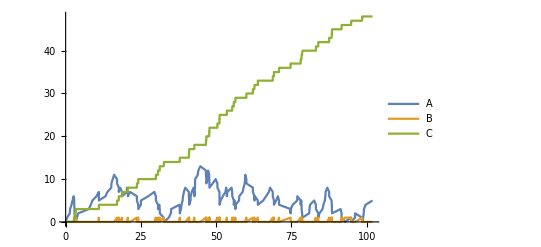

```mathematica
ListLinePlot[{DataTrace[history,A],DataTrace[history,B],DataTrace[history,C]},PlotLegends->{A,B,C}]
```

The second example is a cyclic predator-prey system, aka the rock-paper-scissors oscillator.

```mathematica
Vm=50;  (* volume is V * 1.66 fL when using nM in rate constants *)
CyclicPredatorPrey={
rxninstance[R+P,2P,1/Vm],
rxninstance[P+S,2S,1/Vm],
rxninstance[S+R,2R,1/Vm]
};
initialstate=Vm(R+P+S);
```

```mathematica
history=SimulateReactionSchema[CyclicPredatorPrey,initialstate,10];
```

```mathematica
Take[history,3]~Join~Take[history,-3]//MatrixForm
```

(0 | 50 P+50 R+50 S
0.00691485 | 49 P+50 R+51 S
0.0117942 | 49 P+51 R+50 S
9.99371 | 10 P+42 R+98 S
9.99488 | 9 P+42 R+99 S
10.0011 | 9 P+43 R+98 S)

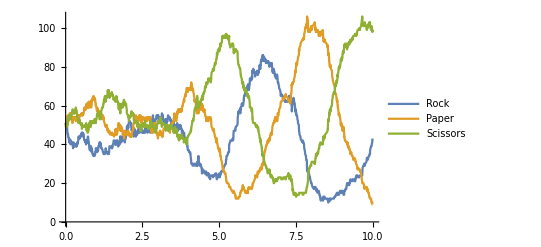

```mathematica
ListLinePlot[{DataTrace[history,R],DataTrace[history,P],DataTrace[history,S]},PlotLegends->{Rock,Paper,Scissors}]
```

It’s important that our simulator matches a pair of identical reactants both when the reaction appears with a coefficient of 2 and when it appears as a pattern in which the same species can match both parts.  Things are working here if we end up with just one A, just one Y, 49 X’s and probably a few Z’s.  -- if we didn’t have HoldAll, this might be simpler --

```mathematica
Vm=50;  (* volume is V * 1.66 fL when using nM in rate constants *)
SingletonCRN={
rxnschema[2A,A+X,1/Vm],
rxnschema[Y[i_]+Y[j_],Y[i+j],1/Vm],
rxnschema[2Y[i_],Z[i],1/Vm]
};
initialstate=Vm A+Vm Y[10];
```

```mathematica
JITReactions[SingletonCRN[[1]],A,A]
```

{rxninstance[2 A,A+X,1/50]}

```mathematica
JITReactions[SingletonCRN[[2]],Y[7],Y[10]]  (* yes, there are two ways these could match, i=7,j=10 and i=10,j=7 *)
```

{rxninstance[Y[7]+Y[10],Y[17],1/50],rxninstance[Y[7]+Y[10],Y[17],1/50]}

```mathematica
JITReactions[SingletonCRN[[2]],Y[10],Y[10]]
```

{rxninstance[2 Y[10],Y[20],1/50],rxninstance[2 Y[10],Y[20],1/50]}

```mathematica
JITReactions[SingletonCRN[[3]],Y[10],Y[10]]
```

{rxninstance[2 Y[10],Z[10],1/50]}

```mathematica
history=SimulateReactionSchema[SingletonCRN,initialstate,200];
```

```mathematica
Take[history,3]~Join~Take[history,-3]//MatrixForm
```

(0 | 50 A+50 Y[10]
0.0035563 | 50 A+48 Y[10]+Z[10]
0.00483573 | 50 A+46 Y[10]+Y[20]+Z[10]
19.8258 | 2 A+48 X+Y[40]+Y[200]+7 Z[10]+3 Z[20]
22.9322 | 2 A+48 X+Y[240]+7 Z[10]+3 Z[20]
41.3398 | A+49 X+Y[240]+7 Z[10]+3 Z[20])

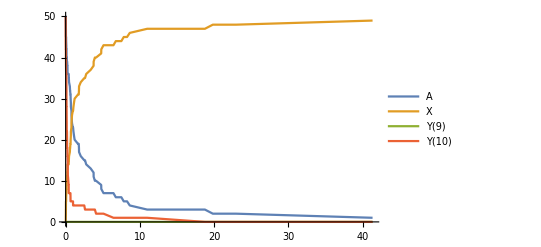

```mathematica
ListLinePlot[{DataTrace[history,A],DataTrace[history,X],DataTrace[history,Y[9]],DataTrace[history,Y[10]]},PlotRange->All,PlotLegends->{A,X,Y[9],Y[10]}]
```

## Simple polymer systems can be straightforward

Here we show the implementation of the polymer example from the introduction.  We can interpret it as saying that polymer nuclei pop in and out of existence with a mean count of 3.7, while monomers can add to polymers with a rate that scales linearly with their length.  This isn’t meant to be realistic for any particular system, but just illustrates some possibilities for how to set up models in the reaction schema simulator.

```mathematica
f[x___]:=0.1(Length[{x}] +5)
PolymerCRN={
rxnschema[0,Poly[],3.7],
rxnschema[Poly[],0,1.0],
rxnschema[M+Poly[x___],Poly[x,M],f[x]]
};
initialstate=50 M;
```

```mathematica
JITPropensities[PolymerCRN,SumToCount[M+Poly[x,M,x]]]
```

{rxnprop[0,Poly[],3.7],rxnprop[M+Poly[x,M,x],Poly[x,M,x,M],0.8]}

```mathematica
JITPropensities[PolymerCRN,SumToCount[initialstate+Poly[]]]
```

{rxnprop[0,Poly[],3.7],rxnprop[Poly[],0,1.],rxnprop[M+Poly[],Poly[M],25.]}

```mathematica
history=SimulateReactionSchema[PolymerCRN,initialstate,10];
```

```mathematica
{First[history],Last[history]}//MatrixForm
```

(0 | 50 M
10.0522 | 4 Poly[]+Poly[M]+Poly[M,M,M,M,M]+Poly[M,M,M,M,M,M,M]+Poly[M,M,M,M,M,M,M,M,M,M,M,M,M]+Poly[M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M,M])

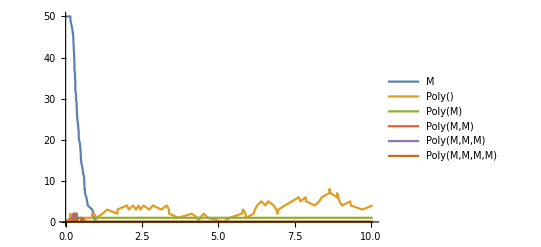

```mathematica
ListLinePlot[{DataTrace[history,M],DataTrace[history,Poly[]],DataTrace[history,Poly[M]],DataTrace[history,Poly[M,M]],DataTrace[history,Poly[M,M,M]],DataTrace[history,Poly[M,M,M,M]]},PlotLegends->{M,Poly[],Poly[M],Poly[M,M],Poly[M,M,M],Poly[M,M,M,M]},PlotRange->All]
```

```mathematica
maxlen[{t_,state_}]:={t,Max[ (List@@Simplify[state/.{c_Integer->1,M->0}])/.Poly[x___]:>Length[{x}] ] }
numpoly[{t_,state_}]:={t,Simplify[state/.{Poly[___]->1,M->0}] }
```

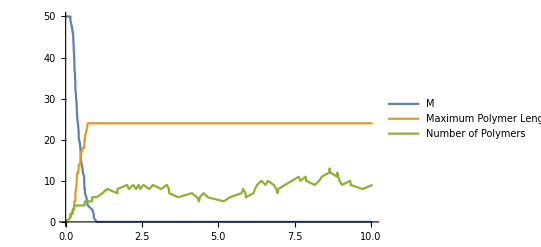

```mathematica
ListLinePlot[{DataTrace[history,M],maxlen/@history,numpoly/@history},PlotLegends->{M,"Maximum Polymer Length","Number of Polymers"}]
```

## A Turing-universal model: Stack machines with abstract polymers

This is the abstract polymer stack machine discussed in “Efficient Turing-Universal Computation with DNA Polymers” (Qian & Winfree, DNA Computing & Molecular Programming, 2011).   The specific example being illustrated is that simply copies the binary string initially on stack 1, placing it (reversed) on stack 2 and stack 3.    Multi-tape stack machines that can push and pop from the stack, branching on empty stacks, are as a general model Turing-universal, and there are small universal stack machines that can efficiently simulate arbitrary Turing machines and other stack machines.  As the Beatles, say, “It’s easy!”

First at the abstract level, as in Figure 4b of that paper:

```mathematica
SMCopySchemata={
rxnschema[S1+Stack1[x___,0],S2+Stack1[x],1],
rxnschema[S1+Stack1[x___,1],S4+Stack1[x],1],
rxnschema[S1+Stack1[],S6+Stack1[],1],
rxnschema[S2+Stack2[x___],S3+Stack2[x,0],1],
rxnschema[S3+Stack3[x___],S1+Stack3[x,0],1],
rxnschema[S4+Stack2[x___],S5+Stack2[x,1],1],
rxnschema[S5+Stack3[x___],S1+Stack3[x,1],1]
};
```

```mathematica
history=SimulateReactionSchema[SMCopySchemata,S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[],100];
```

```mathematica
history//MatrixForm
```

(0 | S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[]
4.59231 | S4+Stack1[0,1,1,0,1,0,0,1,1]+Stack2[]+Stack3[]
5.0124 | S5+Stack1[0,1,1,0,1,0,0,1,1]+Stack2[1]+Stack3[]
5.02281 | S1+Stack1[0,1,1,0,1,0,0,1,1]+Stack2[1]+Stack3[1]
6.90172 | S4+Stack1[0,1,1,0,1,0,0,1]+Stack2[1]+Stack3[1]
7.53236 | S5+Stack1[0,1,1,0,1,0,0,1]+Stack2[1,1]+Stack3[1]
9.24547 | S1+Stack1[0,1,1,0,1,0,0,1]+Stack2[1,1]+Stack3[1,1]
9.70251 | S4+Stack1[0,1,1,0,1,0,0]+Stack2[1,1]+Stack3[1,1]
10.2823 | S5+Stack1[0,1,1,0,1,0,0]+Stack2[1,1,1]+Stack3[1,1]
13.5515 | S1+Stack1[0,1,1,0,1,0,0]+Stack2[1,1,1]+Stack3[1,1,1]
15.0316 | S2+Stack1[0,1,1,0,1,0]+Stack2[1,1,1]+Stack3[1,1,1]
15.2842 | S3+Stack1[0,1,1,0,1,0]+Stack2[1,1,1,0]+Stack3[1,1,1]
15.6197 | S1+Stack1[0,1,1,0,1,0]+Stack2[1,1,1,0]+Stack3[1,1,1,0]
15.8873 | S2+Stack1[0,1,1,0,1]+Stack2[1,1,1,0]+Stack3[1,1,1,0]
16.5042 | S3+Stack1[0,1,1,0,1]+Stack2[1,1,1,0,0]+Stack3[1,1,1,0]
17.1276 | S1+Stack1[0,1,1,0,1]+Stack2[1,1,1,0,0]+Stack3[1,1,1,0,0]
18.6299 | S4+Stack1[0,1,1,0]+Stack2[1,1,1,0,0]+Stack3[1,1,1,0,0]
18.9764 | S5+Stack1[0,1,1,0]+Stack2[1,1,1,0,0,1]+Stack3[1,1,1,0,0]
20.107 | S1+Stack1[0,1,1,0]+Stack2[1,1,1,0,0,1]+Stack3[1,1,1,0,0,1]
20.2679 | S2+Stack1[0,1,1]+Stack2[1,1,1,0,0,1]+Stack3[1,1,1,0,0,1]
21.9386 | S3+Stack1[0,1,1]+Stack2[1,1,1,0,0,1,0]+Stack3[1,1,1,0,0,1]
22.7991 | S1+Stack1[0,1,1]+Stack2[1,1,1,0,0,1,0]+Stack3[1,1,1,0,0,1,0]
22.8797 | S4+Stack1[0,1]+Stack2[1,1,1,0,0,1,0]+Stack3[1,1,1,0,0,1,0]
23.3992 | S5+Stack1[0,1]+Stack2[1,1,1,0,0,1,0,1]+Stack3[1,1,1,0,0,1,0]
23.5289 | S1+Stack1[0,1]+Stack2[1,1,1,0,0,1,0,1]+Stack3[1,1,1,0,0,1,0,1]
24.3849 | S4+Stack1[0]+Stack2[1,1,1,0,0,1,0,1]+Stack3[1,1,1,0,0,1,0,1]
25.0695 | S5+Stack1[0]+Stack2[1,1,1,0,0,1,0,1,1]+Stack3[1,1,1,0,0,1,0,1]
28.2208 | S1+Stack1[0]+Stack2[1,1,1,0,0,1,0,1,1]+Stack3[1,1,1,0,0,1,0,1,1]
28.5012 | S2+Stack1[]+Stack2[1,1,1,0,0,1,0,1,1]+Stack3[1,1,1,0,0,1,0,1,1]
30.9427 | S3+Stack1[]+Stack2[1,1,1,0,0,1,0,1,1,0]+Stack3[1,1,1,0,0,1,0,1,1]
31.6061 | S1+Stack1[]+Stack2[1,1,1,0,0,1,0,1,1,0]+Stack3[1,1,1,0,0,1,0,1,1,0]
31.9771 | S6+Stack1[]+Stack2[1,1,1,0,0,1,0,1,1,0]+Stack3[1,1,1,0,0,1,0,1,1,0])

Then at the level of presumed DNA strand displacement implementation reactions, as in Figure 4d of that paper.  Note that even if a reaction mechanism is intrinsically reversible, the simulator requires separate reactions and reaction schema for each direction.

```mathematica
SMCopyDSDSchemata={
(* the stuff in the section below defines the logic of the machine being implemented, here "COPY" *)
rxninstance[S1+b0on1,S2+Q,1],
rxninstance[S1+b1on1,S4+Q,1],
rxninstance[S1+empty1,S6+empty1,1],
rxninstance[S2+Q,S3+b0on2,1],
rxninstance[S3+Q,S1+b0on3,1],
rxninstance[S4+Q,S5+b1on2,1],
rxninstance[S5+Q,S1+b1on3,1],
(* the stuff below is the same for any three-stack machine *)
rxninstance[Q1,Q,1],rxninstance[Q,Q1,1],
rxninstance[Q2,Q,1],rxninstance[Q,Q2,1],
rxninstance[Q3,Q,1],rxninstance[Q,Q3,1],
rxnschema[Stack1[x___]+b0on1,Stack1[x,0]+Q1,1],rxnschema[Stack1[x___,0]+Q1,Stack1[x]+b0on1,1],
rxnschema[Stack1[x___]+b1on1,Stack1[x,1]+Q1,1],rxnschema[Stack1[x___,1]+Q1,Stack1[x]+b1on1,1],
rxnschema[Stub1[]+empty1,Stack1[]+Q1,1],rxnschema[Stack1[]+Q1,Stub1[]+empty1,1],
rxnschema[Stack2[x___]+b0on2,Stack2[x,0]+Q2,1],rxnschema[Stack2[x___,0]+Q2,Stack2[x]+b0on2,1],
rxnschema[Stack2[x___]+b1on2,Stack2[x,1]+Q2,1],rxnschema[Stack2[x___,1]+Q2,Stack2[x]+b1on2,1],
rxnschema[Stub2[]+empty2,Stack2[]+Q2,1],rxnschema[Stack2[]+Q2,Stub2[]+empty2,1],
rxnschema[Stack3[x___]+b0on3,Stack3[x,0]+Q3,1],rxnschema[Stack3[x___,0]+Q3,Stack3[x]+b0on3,1],
rxnschema[Stack3[x___]+b1on3,Stack3[x,1]+Q3,1],rxnschema[Stack3[x___,1]+Q3,Stack3[x]+b1on3,1],
rxnschema[Stub3[]+empty3,Stack3[]+Q3,1],rxnschema[Stack3[]+Q3,Stub3[]+empty3,1]
};
```

```mathematica
JITPropensities[SMCopyDSDSchemata,SumToCount[Q+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[]]]
```

{rxnprop[Q,Q1,1],rxnprop[Q,Q2,1],rxnprop[Q,Q3,1]}

```mathematica
history=SimulateReactionSchema[SMCopyDSDSchemata,Q+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[],1000];  (* this takes several seconds *)
```

```mathematica
Take[history,10]//MatrixForm
```

(0 | Q+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[]
0.290145 | Q2+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[]
0.584656 | empty2+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack3[]+Stub2[]
2.22372 | Q2+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[]
3.2419 | Q+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[]
3.60577 | Q1+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[]
6.79354 | b1on1+S1+Stack1[0,1,1,0,1,0,0,1,1]+Stack2[]+Stack3[]
6.96425 | Q1+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[]
7.24073 | b1on1+S1+Stack1[0,1,1,0,1,0,0,1,1]+Stack2[]+Stack3[]
7.2992 | Q+S4+Stack1[0,1,1,0,1,0,0,1,1]+Stack2[]+Stack3[])

```mathematica
(* just look at one point per reaction cycle, ignoring fluctuations prior to action being taken *)
First/@SplitBy[Select[history,MemberQ[Last[#],Q]&],Last]//MatrixForm
```

(0 | Q+S1+Stack1[0,1,1,0,1,0,0,1,1,1]+Stack2[]+Stack3[]
7.2992 | Q+S4+Stack1[0,1,1,0,1,0,0,1,1]+Stack2[]+Stack3[]
28.1698 | Q+S5+Stack1[0,1,1,0,1,0,0,1,1]+Stack2[1]+Stack3[]
32.6683 | Q+S1+Stack1[0,1,1,0,1,0,0,1,1]+Stack2[1]+Stack3[1]
38.6106 | Q+S4+Stack1[0,1,1,0,1,0,0,1]+Stack2[1]+Stack3[1]
43.7479 | Q+S5+Stack1[0,1,1,0,1,0,0,1]+Stack2[1,1]+Stack3[1]
52.4329 | Q+S1+Stack1[0,1,1,0,1,0,0,1]+Stack2[1,1]+Stack3[1,1]
54.0458 | Q+S4+Stack1[0,1,1,0,1,0,0]+Stack2[1,1]+Stack3[1,1]
61.0969 | Q+S5+Stack1[0,1,1,0,1,0,0]+Stack2[1,1,1]+Stack3[1,1]
77.486 | Q+S1+Stack1[0,1,1,0,1,0,0]+Stack2[1,1,1]+Stack3[1,1,1]
82.5693 | Q+S2+Stack1[0,1,1,0,1,0]+Stack2[1,1,1]+Stack3[1,1,1]
84.6576 | Q+S3+Stack1[0,1,1,0,1,0]+Stack2[1,1,1,0]+Stack3[1,1,1]
89.0023 | Q+S1+Stack1[0,1,1,0,1,0]+Stack2[1,1,1,0]+Stack3[1,1,1,0]
92.5252 | Q+S2+Stack1[0,1,1,0,1]+Stack2[1,1,1,0]+Stack3[1,1,1,0]
100.546 | Q+S3+Stack1[0,1,1,0,1]+Stack2[1,1,1,0,0]+Stack3[1,1,1,0]
113.584 | Q+S1+Stack1[0,1,1,0,1]+Stack2[1,1,1,0,0]+Stack3[1,1,1,0,0]
138.444 | Q+S4+Stack1[0,1,1,0]+Stack2[1,1,1,0,0]+Stack3[1,1,1,0,0]
147.163 | Q+S5+Stack1[0,1,1,0]+Stack2[1,1,1,0,0,1]+Stack3[1,1,1,0,0]
158.612 | Q+S1+Stack1[0,1,1,0]+Stack2[1,1,1,0,0,1]+Stack3[1,1,1,0,0,1]
183.581 | Q+S2+Stack1[0,1,1]+Stack2[1,1,1,0,0,1]+Stack3[1,1,1,0,0,1]
186.75 | Q+S3+Stack1[0,1,1]+Stack2[1,1,1,0,0,1,0]+Stack3[1,1,1,0,0,1]
191.529 | Q+S1+Stack1[0,1,1]+Stack2[1,1,1,0,0,1,0]+Stack3[1,1,1,0,0,1,0]
226.439 | Q+S4+Stack1[0,1]+Stack2[1,1,1,0,0,1,0]+Stack3[1,1,1,0,0,1,0]
238.145 | Q+S5+Stack1[0,1]+Stack2[1,1,1,0,0,1,0,1]+Stack3[1,1,1,0,0,1,0]
258.189 | Q+S1+Stack1[0,1]+Stack2[1,1,1,0,0,1,0,1]+Stack3[1,1,1,0,0,1,0,1]
280.016 | Q+S4+Stack1[0]+Stack2[1,1,1,0,0,1,0,1]+Stack3[1,1,1,0,0,1,0,1]
296.496 | Q+S5+Stack1[0]+Stack2[1,1,1,0,0,1,0,1,1]+Stack3[1,1,1,0,0,1,0,1]
298.561 | Q+S1+Stack1[0]+Stack2[1,1,1,0,0,1,0,1,1]+Stack3[1,1,1,0,0,1,0,1,1]
334.141 | Q+S2+Stack1[]+Stack2[1,1,1,0,0,1,0,1,1]+Stack3[1,1,1,0,0,1,0,1,1]
343.131 | Q+S3+Stack1[]+Stack2[1,1,1,0,0,1,0,1,1,0]+Stack3[1,1,1,0,0,1,0,1,1]
353.497 | Q+S1+Stack1[]+Stack2[1,1,1,0,0,1,0,1,1,0]+Stack3[1,1,1,0,0,1,0,1,1,0]
365.521 | Q+S6+Stack1[]+Stack2[1,1,1,0,0,1,0,1,1,0]+Stack3[1,1,1,0,0,1,0,1,1,0])

# Examples from Figure 3 of Johnson & Winfree (TCS, 2020)

The Reaction Schema Simulator does not directly simulate (linear) Polymer Reaction Networks as described in the paper.  For example, there is no notion of compatibility relations or a regular expression describing the allowable polymers.   Mathematica’s pattern matching machinery is powerful enough to capture these ideas, but in practice it is seldom necessary.  Usually, without explicit constraints on what species are allowed, the implicit constraints of reachability via valid reactions are sufficient.  Secondly, the Reaction Schema Simulator allows more general representations of molecules -- arbitrary Mathematica expressions -- which sometimes suggests different (and more natural?) forms for the reaction schema as compared to the PRNs given in Figure 3.   It should be clear enough how the reaction schema relate to the PRN schema shown in the figure.

## Dynamic Instability

A simplified model of dynamic instability in microtubules.  In order to track individual polymers, we allow them to have ID tags, e.g. #1 through #11, although to match Figure 3’s PRN, they should all have the same tag.  Tf represents free tubulin bound to GTP.  Df represents free tubulin after the GTP has been hydrolyzed to GDP.  S[i][seq] is microtubule #i with the given sequence of tubulin monomers.

What happens in this model, from the specified initial conditions where there is a lot of Tf in solution along with 11 seeds?  First, all the seeds grow, though at different stochastic rates. After all the Tf has been used up, for a while the microtubule lengths don’t change -- but hydrolysis has begun and is creeping toward the now-stalled growth end.  When the hydrolysis eliminates the cap of T in a polymer, that polymer rapidly disintegrates -- what is called the catastrophe.  This releases a lot of Df into solution, which slowly gets recharged into Tf.  The catastrophe happens at different times for different microtubules; the initially longer microtubules have a higher probability of lasting longer as well, and thus they have a better chance of utilizing the released tubulin to grow even longer still.  Catastrophe often results in the microtubule depolymerizing all the way back to the seed stub, but occasionally there is a “rescue” as new T gets added, recreating the cap and stabilizing the microtubule for further growth.

```mathematica
DynamicPRN={
rxnschema[S[i_][x___]+Tf,S[i][x,T],4.0], (* free tubulin binds to the growing end of the microtubule *)
rxninstance[Df,Tf,2.0], (* free hydrolyzed tubulin can be recharged by metabolic processes *)
rxnschema[S[i_][T,x___],S[i][D,x],80.0], (* hydrolysis of polymerized tubulin, in this simple model, must start at the lagging end of the microtubule *)
rxnschema[S[i_][x___,D,T,y___],S[i][x,D,D,y],80.0], (* polymerized tubulin can hydrolyze if it is adjacent to an already hydrolyzed tubulin *)
rxnschema[S[i_][x___,D],S[i][x]+Df,1000.0] (* if the wave of hydrolysis reaches the growing end, then hydrolyzed tubulin depolymerizes *)
};
initialstate=Sum[S[i][],{i,1,11}]+1000Tf;
```

```mathematica
initialstate
```

1000 Tf+S[1][]+S[2][]+S[3][]+S[4][]+S[5][]+S[6][]+S[7][]+S[8][]+S[9][]+S[10][]+S[11][]

```mathematica
JITPropensities[DynamicPRN,SumToCount[initialstate]]
```

{rxnprop[Tf+S[1][],S[1][T],4000.],rxnprop[Tf+S[2][],S[2][T],4000.],rxnprop[Tf+S[3][],S[3][T],4000.],rxnprop[Tf+S[4][],S[4][T],4000.],rxnprop[Tf+S[5][],S[5][T],4000.],rxnprop[Tf+S[6][],S[6][T],4000.],rxnprop[Tf+S[7][],S[7][T],4000.],rxnprop[Tf+S[8][],S[8][T],4000.],rxnprop[Tf+S[9][],S[9][T],4000.],rxnprop[Tf+S[10][],S[10][T],4000.],rxnprop[Tf+S[11][],S[11][T],4000.]}

```mathematica
(* this can be slow.  be patient.  or decrease the time. *)
Timing[history=SimulateReactionSchema[DynamicPRN,initialstate,10];]
```

{174.315,Null}

```mathematica
Last[history]
```

{10.0008,466 Df+19 Tf+S[1][D,T,T,T]+S[2][T,T]+S[3][D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,T,T,T,T,T,T]+S[4][D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,T,T,T,T,T,T,T]+S[5][D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,T,T,T]+S[6][D,D,T,T,T,T]+S[7][D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,D,T,T,T,T,T]+S[8][D,T,T,T]+S[9][D,D,D,T]+S[10][D,D,D,D,D,D,D,D,D,D,D,D,D,T,T,T,T]+S[11][]}

```mathematica
tubelen[i_][{t_,state_}]:={t,Max[ (Simplify[state/.{Tf->0,Df->0}]/.Plus->List)/.S[j_][x___]:>If[i==j,Length[{x}],0 ]]}
```

```mathematica
tubelen[3][Last[history]]
```

{10.0008,240}

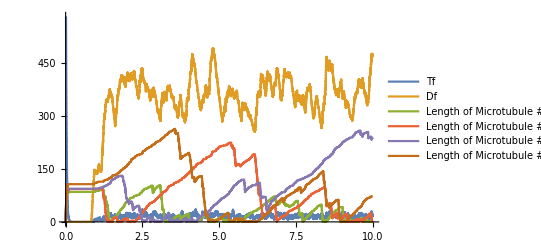

```mathematica
ListLinePlot[{DataTrace[history,Tf],DataTrace[history,Df],tubelen[1]/@history,tubelen[2]/@history,tubelen[3]/@history,tubelen[4]/@history},PlotLegends->{Tf,Df,"Length of Microtubule #1","Length of Microtubule #2","Length of Microtubule #3","Length of Microtubule #4"}]
```

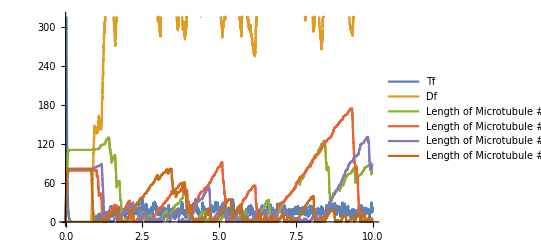

```mathematica
ListLinePlot[{DataTrace[history,Tf],DataTrace[history,Df],tubelen[5]/@history,tubelen[6]/@history,tubelen[7]/@history,tubelen[8]/@history},PlotLegends->{Tf,Df,"Length of Microtubule #5","Length of Microtubule #6","Length of Microtubule #7","Length of Microtubule #8"}]
```

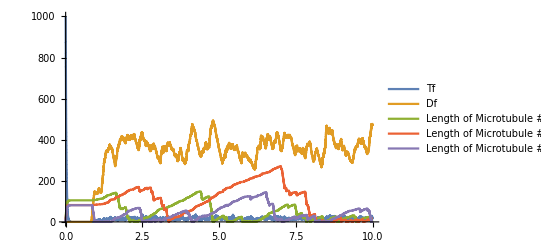

```mathematica
ListLinePlot[{DataTrace[history,Tf],DataTrace[history,Df],tubelen[9]/@history,tubelen[10]/@history,tubelen[11]/@history},PlotLegends->{Tf,Df,"Length of Microtubule #9","Length of Microtubule #10","Length of Microtubule #11"}]
```

## Rock-Paper-Scissors PRN Oscillator

We saw the cyclic predator-prey CRN as one of the first examples in this notebook.  That CRN is also called the rock-paper-scissors oscillator.  The PRN below is NOT that.   But it is a PRN that is inspired by, and in some ways analogous to, the CRN Rock-Paper-Scissors oscillator.  There are just three molecules: a polymer of R, a polymer of P, and a polymer of S.  In the typical dynamics, each cycles through three phases: growing, shrinking, and being stuck at length 1 -- what we call a polymer stub.   The stubs are catalytic: each one catalyzes the growth of one of the other polymers, and catalyzes the shrinkage of the other polymer.   We haven’t done the analysis, but it appears that the total polymer length does some kind of random walk that is slightly biased toward getting larger, so the period and amplitude of this “oscillator” keeps getting larger over time.

```mathematica
OscillatorPRN={
rxnschema[poly[R]+poly[S,x___],poly[R]+poly[S,S,x],1.0], (* stub R catalyzes the growth of S *)
rxnschema[poly[R]+poly[P,P,x___],poly[R]+ poly[P,x], 1.0], (* stub R catalyzes the shrinking of P *)
rxnschema[poly[P]+poly[R,x___],poly[P]+poly[R,R,x],1.0], (* stub P catalyzes the growth of R *)
rxnschema[poly[P]+poly[S,S,x___],poly[P]+ poly[S,x], 1.0], (* stub P catalyzes the shrinking of S *)
rxnschema[poly[S]+poly[P,x___],poly[S]+poly[P,P,x],1.0], (* stub S catalyzes the growth of P *)
rxnschema[poly[S]+poly[R,R,x___],poly[S]+ poly[R,x], 1.0] (* stub S catalyzes the shrinking of R *)
};
initialstate=poly[R]+poly[P]+poly[S];
```

```mathematica
JITPropensities[OscillatorPRN,SumToCount[initialstate]]
```

{rxnprop[poly[P]+poly[R],poly[P]+poly[R,R],1.],rxnprop[poly[P]+poly[S],poly[S]+poly[P,P],1.],rxnprop[poly[R]+poly[S],poly[R]+poly[S,S],1.]}

```mathematica
history=SimulateReactionSchema[OscillatorPRN,initialstate,1000];
```

```mathematica
Last[history]
```

{1000.63,poly[P]+poly[R,R,R,R,R,R]+poly[S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S,S]}

```mathematica
polylen[i_][{t_,state_}]:={t,Plus@@(state/.poly[j_,x___]:>If[i===j,Length[{x}]+1,0 ])}
```

```mathematica
polylen[P][Last[history]]
```

{1000.63,1}

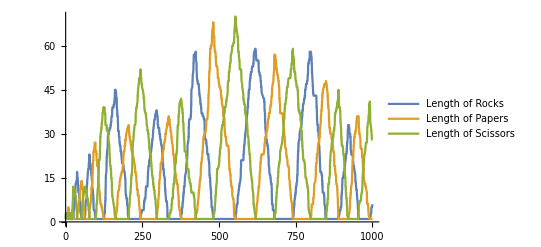

```mathematica
ListLinePlot[{polylen[R]/@history,polylen[P]/@history,polylen[S]/@history},PlotLegends->{"Length of Rocks","Length of Papers","Length of Scissors"}]
```

## Restriction Enzymes

This PRN example is at a higher level of abstraction compared to the DNA sequence level schemata mentioned in the Advanced Tutorial section.

In Figure 3, a trimolecular reaction is used.  Here, we need to break it apart into separate bimolecular reactions.  Not the same, but equivalent in a sense.

The specific initial condition given allows the restriction enzymes and ligases to scramble two DNA molecules to make all 16 combinatorial possibilities.

```mathematica
RestrictionPRN={
rxnschema[R[i_]+DNA[x___,S[i_],y___],R[i]+DNA[x,Sdown[i]]+DNA[Sup[i],y],1.0], (* restrict *)
rxnschema[DNA[x___,Sdown[i_]]+DNA[Sup[i_],y___],DNA[x,s[i],y],1.0], (* associate *)
rxnschema[DNA[x___,s[i_],y___],DNA[x,Sdown[i]]+DNA[Sup[i],y],1.0], (* dissociate *)
rxnschema[L[i_]+DNA[x___,s[i_],y___],L[i]+DNA[x,S[i],y],1.0] (* ligate *)
};
initialstate=R[1]+R[2]+R[3]+L[1]+L[2]+L[3]+10 DNA[A,S[1],B,S[2],C,S[3],D]+10DNA[a,S[1],b,S[2],c,S[3],d];
```

```mathematica
Timing[history=SimulateReactionSchema[RestrictionPRN,initialstate,20]; Length[history]]  (* scramble them! *)
```

{16.393,2452}

```mathematica
Last[history]
```

{20.0127,DNA[a,Sdown[1]]+4 DNA[A,Sdown[1]]+DNA[Sup[3],d]+2 DNA[Sup[3],D]+3 DNA[Sup[1],b,Sdown[2]]+DNA[Sup[2],c,Sdown[3]]+DNA[A,s[1],B,Sdown[2]]+DNA[A,S[1],b,Sdown[2]]+DNA[Sup[2],C,s[3],d]+2 DNA[Sup[2],C,s[3],D]+DNA[Sup[2],C,S[3],D]+DNA[Sup[1],B,s[2],c,Sdown[3]]+DNA[a,s[1],B,S[2],C,Sdown[3]]+DNA[Sup[1],b,S[2],C,S[3],d]+DNA[a,s[1],b,s[2],C,S[3],d]+DNA[a,s[1],B,s[2],c,s[3],D]+DNA[a,s[1],B,S[2],c,s[3],d]+DNA[a,s[1],B,S[2],C,S[3],d]+DNA[a,S[1],b,S[2],c,s[3],d]+DNA[a,S[1],b,S[2],c,S[3],D]+DNA[a,S[1],B,s[2],C,S[3],D]+DNA[a,S[1],B,S[2],c,s[3],d]+DNA[A,s[1],b,S[2],c,s[3],d]+DNA[A,s[1],B,s[2],C,S[3],d]+DNA[A,S[1],b,S[2],c,S[3],D]+DNA[A,S[1],B,S[2],c,s[3],D]+L[1]+L[2]+L[3]+R[1]+R[2]+R[3]}

```mathematica
Timing[history=SimulateReactionSchema[RestrictionPRN,Last[Last[history]/.R[_]->0],10];]  (* ligate them! *)
```

{0.730372,Null}

```mathematica
Last[history]
```

{4.42114,DNA[a,S[1],b,S[2],c,S[3],d]+DNA[a,S[1],b,S[2],c,S[3],D]+DNA[a,S[1],b,S[2],C,S[3],d]+2 DNA[a,S[1],b,S[2],C,S[3],D]+2 DNA[a,S[1],B,S[2],c,S[3],d]+3 DNA[a,S[1],B,S[2],C,S[3],D]+DNA[A,S[1],b,S[2],c,S[3],d]+3 DNA[A,S[1],b,S[2],c,S[3],D]+DNA[A,S[1],b,S[2],C,S[3],d]+DNA[A,S[1],B,S[2],c,S[3],d]+DNA[A,S[1],B,S[2],c,S[3],D]+3 DNA[A,S[1],B,S[2],C,S[3],d]+L[1]+L[2]+L[3]}

## Turing machines

This is the 3-state Busy Beaver from Lin & Rado (1965).
Note that there are some complexities dealing with finite representations of the the tape, such that space at the end of the tape is assumed to be 0 if it’s not there.
A comparison is made to the built-in Mathematica Turing machine simulator.

```mathematica
TMBusyBeaverPRN={
rxnschema[ID[x___,q1,b0r,y___],ID[x,b1l,q2,y],1], rxnschema[ID[x___,q1],ID[x,b1l,q2],1],
rxnschema[ID[x___,q1,b1r,y___],ID[x,b1l,h,y],1],
rxnschema[ID[x___,q2,b0r,y___],ID[x,b0l,q3,y],1], rxnschema[ID[x___,q2],ID[x,b0l,q3],1],
rxnschema[ID[x___,q2,b1r,y___],ID[x,b1l,q2,y],1],
rxnschema[ID[x___,b0l,q3,b0r,y___],ID[x,q3,b0r,b1r,y],1],rxnschema[ID[x___,b0l,q3],ID[x,q3,b0r,b1r],1],
rxnschema[ID[x___,b1l,q3,b0r,y___],ID[x,q3,b1r,b1r,y],1],rxnschema[ID[x___,b1l,q3],ID[x,q3,b1r,b1r],1],
rxnschema[ID[q3,b0r,y___],ID[q3,b0r,b1r,y],1], rxnschema[ID[q3],ID[q3,b0r,b1r],1],
rxnschema[ID[x___,b0l,q3,b1r,y___],ID[x,q1,b0r,b1r,y],1],
rxnschema[ID[x___,b1l,q3,b1r,y___],ID[x,q1,b1r,b1r,y],1],
rxnschema[ID[q3,b1r,y___],ID[q1,b0r,b1r,y],1]
};
```

```mathematica
history=SimulateReactionSchema[TMBusyBeaverPRN,ID[q1],100];
```

```mathematica
history//MatrixForm
```

(0 | ID[q1]
2.74648 | ID[b1l,q2]
3.57009 | ID[b1l,b0l,q3]
3.60929 | ID[b1l,q3,b0r,b1r]
4.13061 | ID[q3,b1r,b1r,b1r]
4.61785 | ID[q1,b0r,b1r,b1r,b1r]
5.5541 | ID[b1l,q2,b1r,b1r,b1r]
6.34494 | ID[b1l,b1l,q2,b1r,b1r]
6.65717 | ID[b1l,b1l,b1l,q2,b1r]
7.57457 | ID[b1l,b1l,b1l,b1l,q2]
7.68379 | ID[b1l,b1l,b1l,b1l,b0l,q3]
8.22103 | ID[b1l,b1l,b1l,b1l,q3,b0r,b1r]
13.5573 | ID[b1l,b1l,b1l,q3,b1r,b1r,b1r]
14.0222 | ID[b1l,b1l,q1,b1r,b1r,b1r,b1r]
14.8954 | ID[b1l,b1l,b1l,h,b1r,b1r,b1r])

```mathematica
TuringMachine[{ {1,0}->{2,1,+1},{1,1}->{0,1,+1},{2,0}->{3,0,+1},{2,1}->{2,1,+1},{3,0}->{3,1,-1},{3,1}->{1,1,-1} },{{1,5},{0,0,0,0,0,0,0,0,0,0,0,0}},20]//MatrixForm
```

({1,5,0} | {0,0,0,0,0,0,0,0,0,0,0,0}
{2,6,1} | {0,0,0,0,1,0,0,0,0,0,0,0}
{3,7,2} | {0,0,0,0,1,0,0,0,0,0,0,0}
{3,6,1} | {0,0,0,0,1,0,1,0,0,0,0,0}
{3,5,0} | {0,0,0,0,1,1,1,0,0,0,0,0}
{1,4,-1} | {0,0,0,0,1,1,1,0,0,0,0,0}
{2,5,0} | {0,0,0,1,1,1,1,0,0,0,0,0}
{2,6,1} | {0,0,0,1,1,1,1,0,0,0,0,0}
{2,7,2} | {0,0,0,1,1,1,1,0,0,0,0,0}
{2,8,3} | {0,0,0,1,1,1,1,0,0,0,0,0}
{3,9,4} | {0,0,0,1,1,1,1,0,0,0,0,0}
{3,8,3} | {0,0,0,1,1,1,1,0,1,0,0,0}
{3,7,2} | {0,0,0,1,1,1,1,1,1,0,0,0}
{1,6,1} | {0,0,0,1,1,1,1,1,1,0,0,0}
{0,7,2} | {0,0,0,1,1,1,1,1,1,0,0,0}
{0,7,2} | {0,0,0,1,1,1,1,1,1,0,0,0}
{0,7,2} | {0,0,0,1,1,1,1,1,1,0,0,0}
{0,7,2} | {0,0,0,1,1,1,1,1,1,0,0,0}
{0,7,2} | {0,0,0,1,1,1,1,1,1,0,0,0}
{0,7,2} | {0,0,0,1,1,1,1,1,1,0,0,0}
{0,7,2} | {0,0,0,1,1,1,1,1,1,0,0,0})

## String copying (one-step model)

This version is slightly simplified from that given in Figure 3 because, in effect, we are utilizing an “augmented PRN”.  

Note that because of lack of Michaelis-Menten saturation, the reaction propensity increases linearly with the number of copies made, with no limit.   That means that instead of the number of DNA copies increasing linearly with time, they increase exponentially with time!  This perhaps-unexpected result is because the average time for step n is 1/n, so the average time to perform n steps (and get n copies of DNA) is t(n)=∑_(i=1)^n 1/n ≃ ln(n).  Inverting, n(t) ≃ e^t.  Consequently, the number of copies in 2 “seconds” is highly variable, and you’ll get very different results each time you run the simulation below.

```mathematica
StringCopyPRN={
rxnschema[P+DNA[x___],P+DNA[x]+DNA[x],1]
};
```

```mathematica
history=SimulateReactionSchema[StringCopyPRN,P+DNA[G,A,T,T,A,C,A],2];
```

```mathematica
history//MatrixForm
```

(0 | P+DNA[G,A,T,T,A,C,A]
0.0377191 | P+2 DNA[G,A,T,T,A,C,A]
1.79577 | P+3 DNA[G,A,T,T,A,C,A]
2.43854 | P+4 DNA[G,A,T,T,A,C,A])

## String copying (local model)

Here, polymerase P scans through the string (upper case only) from left to right, duplicating each letter; the separating enzymes s and S work toward each other and cut the string when they meet.  This results in one upper case copy and one lower case copy.  Since P acts catalytically and there are unavoidable unimolecular steps, a linear increase of the lower-case copies accumulates over time.

```mathematica
LocalStringCopyPRN={
(* polymerase P attaches to the string on the left, leaving a separating enzyme s on the left *)
rxnschema[P+string[A,x___],string[s,P,A,x],1],
rxnschema[P+string[T,x___],string[s,P,T,x],1],
rxnschema[P+string[G,x___],string[s,P,G,x],1],
rxnschema[P+string[C,x___],string[s,P,C,x],1],
(* polymerase P duplicates each letter into an upper case and a lower case copy *)
rxnschema[string[x___,P,A,y___],string[x,a,A,P,y],1],rxnschema[string[x___,P,G,y___],string[x,g,G,P,y],1],
rxnschema[string[x___,P,T,y___],string[x,t,T,P,y],1],rxnschema[string[x___,P,C,y___],string[x,c,C,P,y],1],
(* swap upper and lower case *)
rxnschema[string[x___,A,a,y___],string[x,a,A,y],1],rxnschema[string[x___,A,t,y___],string[x,t,A,y],1],
rxnschema[string[x___,A,c,y___],string[x,c,A,y],1],rxnschema[string[x___,A,g,y___],string[x,g,A,y],1],
rxnschema[string[x___,T,a,y___],string[x,a,T,y],1],rxnschema[string[x___,T,t,y___],string[x,t,T,y],1],
rxnschema[string[x___,T,c,y___],string[x,c,T,y],1],rxnschema[string[x___,T,g,y___],string[x,g,T,y],1],
rxnschema[string[x___,G,a,y___],string[x,a,G,y],1],rxnschema[string[x___,G,t,y___],string[x,t,G,y],1],
rxnschema[string[x___,G,c,y___],string[x,c,G,y],1],rxnschema[string[x___,G,g,y___],string[x,g,G,y],1],
rxnschema[string[x___,C,a,y___],string[x,a,C,y],1],rxnschema[string[x___,C,t,y___],string[x,t,C,y],1],
rxnschema[string[x___,C,c,y___],string[x,c,C,y],1],rxnschema[string[x___,C,g,y___],string[x,g,C,y],1],
(* polymerase P dissociates after it has traversed the whole string, leaving a separating enzyme S on the right *)
rxnschema[string[x___,P],string[x,S]+P,1], rxnschema[string[x___,s,S,y___],string[x]+string[y],1],
(* separating enzyme S moves backward through the string, but only through the upper case; conversely for s *)
rxnschema[string[x___,A,S,y___],string[x,S,A,y],1],rxnschema[string[x___,s,a,y___],string[x,a,s,y],1],
rxnschema[string[x___,T,S,y___],string[x,S,T,y],1],rxnschema[string[x___,s,t,y___],string[x,t,s,y],1],
rxnschema[string[x___,G,S,y___],string[x,S,G,y],1],rxnschema[string[x___,s,g,y___],string[x,g,s,y],1],
rxnschema[string[x___,C,S,y___],string[x,S,C,y],1],rxnschema[string[x___,s,c,y___],string[x,c,s,y],1]
};
```

```mathematica
history=SimulateReactionSchema[LocalStringCopyPRN,P+string[G,A,T,T,A,C,A],100];
```

```mathematica
history//MatrixForm
```

(0 | P+string[G,A,T,T,A,C,A]
0.0251941 | string[s,P,G,A,T,T,A,C,A]
0.38169 | string[s,g,G,P,A,T,T,A,C,A]
0.830229 | string[s,g,G,a,A,P,T,T,A,C,A]
1.06125 | string[s,g,a,G,A,P,T,T,A,C,A]
1.3196 | string[s,g,a,G,A,t,T,P,T,A,C,A]
1.41265 | string[g,s,a,G,A,t,T,P,T,A,C,A]
1.48563 | string[g,s,a,G,A,t,T,t,T,P,A,C,A]
1.62076 | string[g,s,a,G,A,t,T,t,T,a,A,P,C,A]
1.94346 | string[g,s,a,G,A,t,t,T,T,a,A,P,C,A]
2.22942 | string[g,a,s,G,A,t,t,T,T,a,A,P,C,A]
2.41026 | string[g,a,s,G,t,A,t,T,T,a,A,P,C,A]
2.4296 | string[g,a,s,G,t,A,t,T,a,T,A,P,C,A]
4.38693 | string[g,a,s,G,t,t,A,T,a,T,A,P,C,A]
4.4566 | string[g,a,s,t,G,t,A,T,a,T,A,P,C,A]
4.61259 | string[g,a,t,s,G,t,A,T,a,T,A,P,C,A]
4.92784 | string[g,a,t,s,G,t,A,T,a,T,A,c,C,P,A]
5.42634 | string[g,a,t,s,G,t,A,a,T,T,A,c,C,P,A]
5.53855 | string[g,a,t,s,G,t,A,a,T,T,c,A,C,P,A]
5.65625 | string[g,a,t,s,G,t,A,a,T,T,c,A,C,a,A,P]
5.86127 | string[g,a,t,s,G,t,A,a,T,T,c,A,a,C,A,P]
5.98627 | string[g,a,t,s,G,t,A,a,T,T,c,a,A,C,A,P]
6.47156 | string[g,a,t,s,t,G,A,a,T,T,c,a,A,C,A,P]
6.48763 | P+string[g,a,t,s,t,G,A,a,T,T,c,a,A,C,A,S]
6.64505 | P+string[g,a,t,s,t,G,a,A,T,T,c,a,A,C,A,S]
6.89313 | P+string[g,a,t,t,s,G,a,A,T,T,c,a,A,C,A,S]
6.90928 | P+string[g,a,t,t,s,G,a,A,T,T,c,a,A,C,S,A]
7.41693 | P+string[g,a,t,t,s,a,G,A,T,T,c,a,A,C,S,A]
7.62555 | P+string[g,a,t,t,s,a,G,A,T,T,c,a,A,S,C,A]
7.73791 | P+string[g,a,t,t,a,s,G,A,T,T,c,a,A,S,C,A]
8.75155 | P+string[g,a,t,t,a,s,G,A,T,T,c,a,S,A,C,A]
13.9893 | P+string[g,a,t,t,a,s,G,A,T,c,T,a,S,A,C,A]
14.4939 | P+string[g,a,t,t,a,s,G,A,T,c,a,T,S,A,C,A]
15.6194 | P+string[g,a,t,t,a,s,G,A,T,c,a,S,T,A,C,A]
16.2611 | P+string[g,a,t,t,a,s,G,A,c,T,a,S,T,A,C,A]
16.3414 | P+string[g,a,t,t,a,s,G,c,A,T,a,S,T,A,C,A]
16.7783 | P+string[g,a,t,t,a,s,c,G,A,T,a,S,T,A,C,A]
17.5134 | P+string[g,a,t,t,a,c,s,G,A,T,a,S,T,A,C,A]
17.8438 | P+string[g,a,t,t,a,c,s,G,A,a,T,S,T,A,C,A]
19.1122 | P+string[g,a,t,t,a,c,s,G,A,a,S,T,T,A,C,A]
20.0242 | P+string[g,a,t,t,a,c,s,G,a,A,S,T,T,A,C,A]
20.8947 | P+string[g,a,t,t,a,c,s,a,G,A,S,T,T,A,C,A]
21.4604 | P+string[g,a,t,t,a,c,a,s,G,A,S,T,T,A,C,A]
21.7594 | P+string[g,a,t,t,a,c,a,s,G,S,A,T,T,A,C,A]
22.5045 | P+string[g,a,t,t,a,c,a,s,S,G,A,T,T,A,C,A]
22.824 | P+string[g,a,t,t,a,c,a]+string[G,A,T,T,A,C,A]
24.0762 | string[g,a,t,t,a,c,a]+string[s,P,G,A,T,T,A,C,A]
25.4387 | string[g,a,t,t,a,c,a]+string[s,g,G,P,A,T,T,A,C,A]
25.5537 | string[g,a,t,t,a,c,a]+string[s,g,G,a,A,P,T,T,A,C,A]
25.605 | string[g,a,t,t,a,c,a]+string[s,g,a,G,A,P,T,T,A,C,A]
25.6177 | string[g,a,t,t,a,c,a]+string[s,g,a,G,A,t,T,P,T,A,C,A]
25.8554 | string[g,a,t,t,a,c,a]+string[s,g,a,G,t,A,T,P,T,A,C,A]
25.8966 | string[g,a,t,t,a,c,a]+string[s,g,a,t,G,A,T,P,T,A,C,A]
28.0403 | string[g,a,t,t,a,c,a]+string[s,g,a,t,G,A,T,t,T,P,A,C,A]
28.3027 | string[g,a,t,t,a,c,a]+string[s,g,a,t,G,A,t,T,T,P,A,C,A]
28.8004 | string[g,a,t,t,a,c,a]+string[s,g,a,t,G,A,t,T,T,a,A,P,C,A]
29.575 | string[g,a,t,t,a,c,a]+string[s,g,a,t,G,A,t,T,T,a,A,c,C,P,A]
29.6018 | string[g,a,t,t,a,c,a]+string[s,g,a,t,G,A,t,T,a,T,A,c,C,P,A]
30.3312 | string[g,a,t,t,a,c,a]+string[s,g,a,t,G,A,t,T,a,T,A,c,C,a,A,P]
30.4779 | P+string[g,a,t,t,a,c,a]+string[s,g,a,t,G,A,t,T,a,T,A,c,C,a,A,S]
30.5092 | P+string[g,a,t,t,a,c,a]+string[g,s,a,t,G,A,t,T,a,T,A,c,C,a,A,S]
30.5633 | P+string[g,a,t,t,a,c,a]+string[g,s,a,t,G,A,t,T,a,T,A,c,C,a,S,A]
30.8189 | P+string[g,a,t,t,a,c,a]+string[g,s,a,t,G,A,t,T,a,T,A,c,a,C,S,A]
30.8502 | P+string[g,a,t,t,a,c,a]+string[g,s,a,t,G,t,A,T,a,T,A,c,a,C,S,A]
31.1302 | P+string[g,a,t,t,a,c,a]+string[g,s,a,t,G,t,A,a,T,T,A,c,a,C,S,A]
31.3898 | P+string[g,a,t,t,a,c,a]+string[g,s,a,t,t,G,A,a,T,T,A,c,a,C,S,A]
31.5646 | P+string[g,a,t,t,a,c,a]+string[g,s,a,t,t,G,A,a,T,T,A,c,a,S,C,A]
32.2888 | P+string[g,a,t,t,a,c,a]+string[g,a,s,t,t,G,A,a,T,T,A,c,a,S,C,A]
32.9987 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,T,T,A,c,a,S,C,A]
33.4117 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,T,T,c,A,a,S,C,A]
33.4758 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,T,c,T,A,a,S,C,A]
33.8696 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,c,T,T,A,a,S,C,A]
34.2595 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,c,T,T,a,A,S,C,A]
34.2991 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,c,T,T,a,S,A,C,A]
34.5188 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,a,A,c,T,T,a,S,A,C,A]
34.5738 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,a,A,c,T,a,T,S,A,C,A]
34.6675 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,a,G,A,c,T,a,T,S,A,C,A]
35.7941 | P+string[g,a,t,t,a,c,a]+string[g,a,t,s,t,a,G,A,c,a,T,T,S,A,C,A]
36.2573 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,G,A,c,a,T,T,S,A,C,A]
36.4651 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,G,A,c,a,T,S,T,A,C,A]
36.5914 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,G,c,A,a,T,S,T,A,C,A]
36.6998 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,G,c,A,a,T,S,T,A,C,A]
36.7199 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,G,c,A,a,S,T,T,A,C,A]
37.5183 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,c,G,A,a,S,T,T,A,C,A]
38.5673 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,c,G,a,A,S,T,T,A,C,A]
38.6454 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,G,a,A,S,T,T,A,C,A]
38.9652 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,G,a,S,A,T,T,A,C,A]
39.2631 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,a,G,S,A,T,T,A,C,A]
40.0319 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,a,S,G,A,T,T,A,C,A]
40.5734 | P+string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,a,s,S,G,A,T,T,A,C,A]
42.8014 | P+2 string[g,a,t,t,a,c,a]+string[G,A,T,T,A,C,A]
46.4711 | 2 string[g,a,t,t,a,c,a]+string[s,P,G,A,T,T,A,C,A]
47.227 | 2 string[g,a,t,t,a,c,a]+string[s,g,G,P,A,T,T,A,C,A]
47.3648 | 2 string[g,a,t,t,a,c,a]+string[s,g,G,a,A,P,T,T,A,C,A]
47.3731 | 2 string[g,a,t,t,a,c,a]+string[s,g,G,a,A,t,T,P,T,A,C,A]
47.4433 | 2 string[g,a,t,t,a,c,a]+string[g,s,G,a,A,t,T,P,T,A,C,A]
47.6642 | 2 string[g,a,t,t,a,c,a]+string[g,s,a,G,A,t,T,P,T,A,C,A]
47.9206 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,G,A,t,T,P,T,A,C,A]
47.9615 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,G,t,A,T,P,T,A,C,A]
48.2718 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,G,t,A,T,t,T,P,A,C,A]
48.7818 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,G,t,A,t,T,T,P,A,C,A]
48.8591 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,G,t,A,t,T,T,a,A,P,C,A]
49.5008 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,G,t,A,t,T,T,a,A,c,C,P,A]
49.7796 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,G,t,t,A,T,T,a,A,c,C,P,A]
49.8812 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,t,G,t,A,T,T,a,A,c,C,P,A]
50.0127 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,t,G,t,A,T,T,a,A,c,C,a,A,P]
50.4686 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,t,G,t,A,T,T,a,c,A,C,a,A,P]
50.8169 | 2 string[g,a,t,t,a,c,a]+string[g,a,s,t,t,G,A,T,T,a,c,A,C,a,A,P]
51.215 | P+2 string[g,a,t,t,a,c,a]+string[g,a,s,t,t,G,A,T,T,a,c,A,C,a,A,S]
51.296 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,T,T,a,c,A,C,a,A,S]
51.4761 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,T,a,T,c,A,C,a,A,S]
51.5375 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,T,T,c,A,C,a,A,S]
51.7007 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,T,T,c,A,a,C,A,S]
51.8748 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,T,T,c,A,a,C,S,A]
52.0938 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,T,c,T,A,a,C,S,A]
52.0997 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,T,c,T,A,a,S,C,A]
52.1909 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,T,c,T,a,A,S,C,A]
52.2292 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,c,T,T,a,A,S,C,A]
52.2587 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,A,a,c,T,a,T,A,S,C,A]
52.2996 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,G,A,a,c,T,a,T,A,S,C,A]
52.4064 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,G,A,a,c,a,T,T,A,S,C,A]
52.7015 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,G,A,a,c,a,T,T,S,A,C,A]
52.7342 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,G,A,a,c,a,T,S,T,A,C,A]
53.2916 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,G,A,a,c,a,S,T,T,A,C,A]
56.9557 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,G,a,A,c,a,S,T,T,A,C,A]
57.1798 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,G,A,c,a,S,T,T,A,C,A]
57.511 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,G,c,A,a,S,T,T,A,C,A]
57.7235 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,G,c,a,A,S,T,T,A,C,A]
57.8402 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,c,G,a,A,S,T,T,A,C,A]
57.9054 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,c,G,a,A,S,T,T,A,C,A]
58.3821 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,c,a,G,A,S,T,T,A,C,A]
59.6459 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,c,a,G,S,A,T,T,A,C,A]
59.9475 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,a,G,S,A,T,T,A,C,A]
59.9919 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,a,S,G,A,T,T,A,C,A]
62.6613 | P+2 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,a,s,S,G,A,T,T,A,C,A]
65.4609 | P+3 string[g,a,t,t,a,c,a]+string[G,A,T,T,A,C,A]
65.476 | 3 string[g,a,t,t,a,c,a]+string[s,P,G,A,T,T,A,C,A]
66.138 | 3 string[g,a,t,t,a,c,a]+string[s,g,G,P,A,T,T,A,C,A]
66.4102 | 3 string[g,a,t,t,a,c,a]+string[g,s,G,P,A,T,T,A,C,A]
67.9246 | 3 string[g,a,t,t,a,c,a]+string[g,s,G,a,A,P,T,T,A,C,A]
68.4635 | 3 string[g,a,t,t,a,c,a]+string[g,s,a,G,A,P,T,T,A,C,A]
68.821 | 3 string[g,a,t,t,a,c,a]+string[g,a,s,G,A,P,T,T,A,C,A]
69.8166 | 3 string[g,a,t,t,a,c,a]+string[g,a,s,G,A,t,T,P,T,A,C,A]
69.9659 | 3 string[g,a,t,t,a,c,a]+string[g,a,s,G,t,A,T,P,T,A,C,A]
70.4157 | 3 string[g,a,t,t,a,c,a]+string[g,a,s,G,t,A,T,t,T,P,A,C,A]
70.4287 | 3 string[g,a,t,t,a,c,a]+string[g,a,s,t,G,A,T,t,T,P,A,C,A]
70.5398 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,A,T,t,T,P,A,C,A]
70.9082 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,A,t,T,T,P,A,C,A]
71.3354 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,A,T,T,P,A,C,A]
71.399 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,A,T,T,a,A,P,C,A]
71.4062 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,A,T,a,T,A,P,C,A]
71.5003 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,A,a,T,T,A,P,C,A]
71.9321 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,a,A,T,T,A,P,C,A]
72.64 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,a,A,T,T,A,P,C,A]
72.9687 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,a,A,T,T,A,c,C,P,A]
72.9944 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,a,A,T,T,c,A,C,P,A]
73.0099 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,a,A,T,T,c,A,C,a,A,P]
73.1695 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,a,A,T,c,T,A,C,a,A,P]
73.1986 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,a,A,T,c,T,A,a,C,A,P]
73.3936 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,G,a,A,T,c,T,A,a,C,A,P]
73.7942 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,G,a,A,T,c,T,a,A,C,A,P]
74.1688 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,G,A,T,c,T,a,A,C,A,P]
74.2342 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,G,A,T,c,a,T,A,C,A,P]
75.3131 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,G,A,T,c,a,T,A,C,A,P]
75.3312 | 3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,G,A,c,T,a,T,A,C,A,P]
75.7227 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,G,A,c,T,a,T,A,C,A,S]
76.1288 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,G,A,c,T,a,T,A,C,S,A]
76.1558 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,G,A,c,a,T,T,A,C,S,A]
76.2708 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,G,c,A,a,T,T,A,C,S,A]
76.4107 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,c,G,A,a,T,T,A,C,S,A]
76.8644 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,s,c,G,A,a,T,T,A,S,C,A]
77.891 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,G,A,a,T,T,A,S,C,A]
78.2817 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,G,A,a,T,T,S,A,C,A]
78.7828 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,G,a,A,T,T,S,A,C,A]
79.704 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,s,a,G,A,T,T,S,A,C,A]
80.0003 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,a,s,G,A,T,T,S,A,C,A]
83.2937 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,a,s,G,A,T,S,T,A,C,A]
83.4762 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,a,s,G,A,S,T,T,A,C,A]
86.1496 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,a,s,G,S,A,T,T,A,C,A]
90.4623 | P+3 string[g,a,t,t,a,c,a]+string[g,a,t,t,a,c,a,s,S,G,A,T,T,A,C,A]
93.1284 | P+4 string[g,a,t,t,a,c,a]+string[G,A,T,T,A,C,A]
94.0928 | 4 string[g,a,t,t,a,c,a]+string[s,P,G,A,T,T,A,C,A]
94.6303 | 4 string[g,a,t,t,a,c,a]+string[s,g,G,P,A,T,T,A,C,A]
94.6644 | 4 string[g,a,t,t,a,c,a]+string[s,g,G,a,A,P,T,T,A,C,A]
94.7113 | 4 string[g,a,t,t,a,c,a]+string[s,g,G,a,A,t,T,P,T,A,C,A]
95.011 | 4 string[g,a,t,t,a,c,a]+string[s,g,a,G,A,t,T,P,T,A,C,A]
95.1381 | 4 string[g,a,t,t,a,c,a]+string[g,s,a,G,A,t,T,P,T,A,C,A]
95.8935 | 4 string[g,a,t,t,a,c,a]+string[g,s,a,G,t,A,T,P,T,A,C,A]
96.0151 | 4 string[g,a,t,t,a,c,a]+string[g,a,s,G,t,A,T,P,T,A,C,A]
96.1934 | 4 string[g,a,t,t,a,c,a]+string[g,a,s,t,G,A,T,P,T,A,C,A]
96.8312 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,A,T,P,T,A,C,A]
96.86 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,A,T,t,T,P,A,C,A]
96.9114 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,A,t,T,T,P,A,C,A]
97.2602 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,A,t,T,T,a,A,P,C,A]
97.3405 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,A,t,T,a,T,A,P,C,A]
97.4386 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,A,T,a,T,A,P,C,A]
97.7989 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,A,T,a,T,A,c,C,P,A]
97.9378 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,A,a,T,T,A,c,C,P,A]
98.2003 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,A,a,T,T,A,c,C,a,A,P]
98.2252 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,A,a,T,T,c,A,C,a,A,P]
98.2519 | 4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,a,A,T,T,c,A,C,a,A,P]
98.759 | P+4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,a,A,T,T,c,A,C,a,A,S]
98.9282 | P+4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,a,A,T,T,c,A,C,a,S,A]
99.1323 | P+4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,a,A,T,T,c,A,a,C,S,A]
99.2466 | P+4 string[g,a,t,t,a,c,a]+string[g,a,t,s,G,t,a,A,T,T,c,a,A,C,S,A]
99.3646 | P+4 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,G,a,A,T,T,c,a,A,C,S,A]
99.7667 | P+4 string[g,a,t,t,a,c,a]+string[g,a,t,s,t,a,G,A,T,T,c,a,A,C,S,A]
100.171 | P+4 string[g,a,t,t,a,c,a]+string[g,a,t,t,s,a,G,A,T,T,c,a,A,C,S,A])

## String equality detection (one-step model)

OK, OK, in Figure 3 the strings were from (0|1)* | Y, while here Y is not a string and we use A, T, G, C ... whatever.

```mathematica
StringEqualityPRN={
rxnschema[string[x___]+string[x___],Y,1]
};
```

```mathematica
(* funny thing here.  pattern matching for stoichiometry 2 reactions is done under Hold, so there are two ways to assign 2 identical objects to 2 identical x patterns. *)
(* there would have been only one way if we had written the LHS pattern as 2 string[x___]. *)
(* adjust rate constant appropriately when this kind of thing arises. *)
JITPropensities[StringEqualityPRN,SumToCount[string[G,A,T,T,A,C,A]+string[G,A,T,T,A,C,A]]]
```

{rxnprop[2 string[G,A,T,T,A,C,A],Y,2],rxnprop[2 string[G,A,T,T,A,C,A],Y,2]}

```mathematica
history=SimulateReactionSchema[StringEqualityPRN,string[G,A,T,T,A,C,A]+string[G,A,T,T,A,C,A],10]
```

{{0,2 string[G,A,T,T,A,C,A]},{0.0273963,Y}}

```mathematica
history=SimulateReactionSchema[StringEqualityPRN,string[G,A,T,T,A,C,A]+string[C,A,T,C,A,T,C,A,T],10]
```

{{0,string[G,A,T,T,A,C,A]+string[C,A,T,C,A,T,C,A,T]}}

## String reverse equality detection (local model)

This time we’ll stick with the given alphabet, close enough... Here, we compare a string of “left-facing” 0 and 1 (l0 and l1) with string of “right-facing” 0 and 1 (r0 and r1), producing the string Y if they are the reverse of each other.  If they are not the reverse of each other, then things get stuck in some intermediate.  Exercise to the reader: modify the schemata so that the original strings are recovered without destruction if they don’t match.

```mathematica
LocalStringReversePRN={
(* polymerase P duplicates each letter into an upper case and a lower case copy *)
rxnschema[string[x___,l0]+string[r0,y___],string[x,S,y],1],
rxnschema[string[x___,l1]+string[r1,y___],string[x,S,y],1],
rxnschema[string[x___,l0,S,r0,y___],string[x,S,y],1],
rxnschema[string[x___,l1,S,r1,y___],string[x,S,y],1],
rxninstance[string[S],string[Y],1]
};
```

```mathematica
SimulateReactionSchema[LocalStringReversePRN,string[l0,l0,l1,l1,l1,l0]+string[r0,r1,r1,r1,r0,r0],10] //MatrixForm
```

(0 | string[l0,l0,l1,l1,l1,l0]+string[r0,r1,r1,r1,r0,r0]
0.073537 | string[l0,l0,l1,l1,l1,S,r1,r1,r1,r0,r0]
0.316974 | string[l0,l0,l1,l1,S,r1,r1,r0,r0]
2.46201 | string[l0,l0,l1,S,r1,r0,r0]
2.59862 | string[l0,l0,S,r0,r0]
2.68165 | string[l0,S,r0]
3.06484 | string[S]
4.26965 | string[Y])

```mathematica
SimulateReactionSchema[LocalStringReversePRN, string[l0, l0, l1, l1, l1, l0] + string[r0, r1, r1, r1, r0], 10]//MatrixForm
```

(0 | string[r0,r1,r1,r1,r0]+string[l0,l0,l1,l1,l1,l0]
0.708586 | string[l0,l0,l1,l1,l1,S,r1,r1,r1,r0]
2.46323 | string[l0,l0,l1,l1,S,r1,r1,r0]
2.70663 | string[l0,l0,l1,S,r1,r0]
2.7594 | string[l0,l0,S,r0]
3.78915 | string[l0,S])

```mathematica
SimulateReactionSchema[LocalStringReversePRN,string[l0,l0,l0,l1,l0,l1,l0]+string[r0,r1,r0,r1,r1,r0,r0],10]//MatrixForm
```

(0 | string[l0,l0,l0,l1,l0,l1,l0]+string[r0,r1,r0,r1,r1,r0,r0]
0.579282 | string[l0,l0,l0,l1,l0,l1,S,r1,r0,r1,r1,r0,r0]
1.10512 | string[l0,l0,l0,l1,l0,S,r0,r1,r1,r0,r0]
3.32874 | string[l0,l0,l0,l1,S,r1,r1,r0,r0]
3.5909 | string[l0,l0,l0,S,r1,r0,r0])

## Polymer Binary Counter

The “counter” molecular C keeps passing through the binary string, from right to left -- each time converting a series of 1s to 0s and converting the first 0 to a 1.  What more do you need?

```mathematica
CounterPRN={
rxnschema[binary[x___,0]+C,binary[x,0,C],1.0], 
rxnschema[binary[x___,1]+C,binary[x,1,C],1.0],
rxnschema[binary[x___,0,C,y___],binary[x,1,y]+C,1.0],
rxnschema[binary[x___,1,C,y___],binary[x,C,0,y],1.0],
rxnschema[binary[C,x___],binary[x]+C,1.0]
};
initialstate=C+binary[0,0,0,0];
```

```mathematica
SimulateReactionSchema[CounterPRN,initialstate,10]//MatrixForm
```

(0 | C+binary[0,0,0,0]
2.8005 | binary[0,0,0,0,C]
3.26354 | C+binary[0,0,0,1]
6.41893 | binary[0,0,0,1,C]
7.49167 | binary[0,0,0,C,0]
7.70909 | C+binary[0,0,1,0]
8.96971 | binary[0,0,1,0,C]
9.99851 | C+binary[0,0,1,1]
11.4293 | binary[0,0,1,1,C])

```mathematica
history=SimulateReactionSchema[CounterPRN,initialstate,150];
```

```mathematica
Select[history,Head[Last[#]]===Plus&]//MatrixForm
```

(0 | C+binary[0,0,0,0]
3.878 | C+binary[0,0,0,1]
5.14632 | C+binary[0,0,1,0]
5.42887 | C+binary[0,0,1,1]
10.8141 | C+binary[0,1,0,0]
11.7962 | C+binary[0,1,0,1]
14.8376 | C+binary[0,1,1,0]
20.1219 | C+binary[0,1,1,1]
26.2574 | C+binary[1,0,0,0]
28.7672 | C+binary[1,0,0,1]
29.9732 | C+binary[1,0,1,0]
31.5687 | C+binary[1,0,1,1]
34.1816 | C+binary[1,1,0,0]
34.5022 | C+binary[1,1,0,1]
36.5517 | C+binary[1,1,1,0]
41.3768 | C+binary[1,1,1,1]
48.6541 | C+binary[0,0,0,0]
51.9579 | C+binary[0,0,0,1]
56.7947 | C+binary[0,0,1,0]
58.1674 | C+binary[0,0,1,1]
63.93 | C+binary[0,1,0,0]
66.5186 | C+binary[0,1,0,1]
69.0234 | C+binary[0,1,1,0]
69.7083 | C+binary[0,1,1,1]
73.3067 | C+binary[1,0,0,0]
75.2648 | C+binary[1,0,0,1]
78.7069 | C+binary[1,0,1,0]
80.0875 | C+binary[1,0,1,1]
86.3 | C+binary[1,1,0,0]
92.198 | C+binary[1,1,0,1]
94.4534 | C+binary[1,1,1,0]
96.0668 | C+binary[1,1,1,1]
101.345 | C+binary[0,0,0,0]
103.83 | C+binary[0,0,0,1]
107.543 | C+binary[0,0,1,0]
110.371 | C+binary[0,0,1,1]
115.915 | C+binary[0,1,0,0]
117.184 | C+binary[0,1,0,1]
120.329 | C+binary[0,1,1,0]
122.191 | C+binary[0,1,1,1]
125.283 | C+binary[1,0,0,0]
127.542 | C+binary[1,0,0,1]
132.516 | C+binary[1,0,1,0]
133.127 | C+binary[1,0,1,1]
139.871 | C+binary[1,1,0,0]
143.798 | C+binary[1,1,0,1]
144.963 | C+binary[1,1,1,0]
147.903 | C+binary[1,1,1,1])

```mathematica
countervalue[{t_,state_}]:={t,Simplify[state//.{C->0,binary[x___]:>FromDigits[{x},2]}]}
```

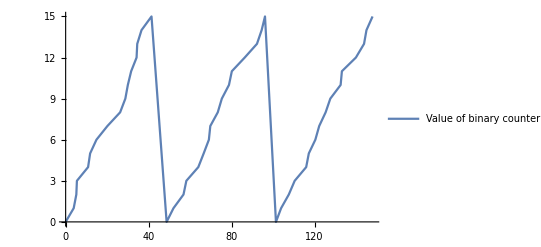

```mathematica
ListLinePlot[countervalue/@Select[history,Head[Last[#]]===Plus&],PlotLegends->{"Value of binary counter"}]
```

# Advanced Tutorial examples

## More reliable polymer oscillators

Compared to the formal (linear) PRNs discussed in the paper, the Reaction Schema Simulator has more flexibility about how to represent species.  Here we re-implement the OscillatorPRN to use integers representing the polymer length, rather than using a homogenous unary string for polymers of each type.  It’s a more concise representation for the same underlying infinite-species CRN.  Maybe you like it better, maybe you don’t, but it is a nice illustration of ways to use the simulator.

In this section, we will also ponder how PRNs might be able to “do things better” than CRNs -- for example, are they capable of more efficiently implementing good oscillators, just as they are more efficient at implement Turing machines?

So how good is the OscillatorPRN aka PolymerRockPaperScissors?  To estimate its phase accuracy, consider that “steady” depolymerization of N monomers will take time proportional to N +/- Sqrt(N), which can be made into an arbitrarily good timer, percentage-wise.  If typically just one of the three polymers, R[ ], P[ ], and S[ ], is minimal length, then the stub can shrink one of the other polymers while growing the third -- in a cyclic pattern.  When R is a stub, P shrinks, and S grows;  when P becomes a stub, then S will shrink and R will grow; and when S becomes a stub, then R will shrink and P will grow.  

This works, but because the total length of polymer is stochastic, the amplitude/frequency does some kind of random walk -- which we often see in a long simulation.

```mathematica
PolymerRockPaperScissors={
rxnschema[R[0]+P[n_?(#>0&)],R[0]+P[n-1],1],
rxnschema[R[0]+S[n_],R[0]+S[n+1],1],
rxnschema[P[0]+S[n_?(#>0&)],P[0]+S[n-1],1],
rxnschema[P[0]+R[n_],P[0]+R[n+1],1],
rxnschema[S[0]+R[n_?(#>0&)],S[0]+R[n-1],1],
rxnschema[S[0]+P[n_],S[0]+P[n+1],1]
};
```

```mathematica
(* this is quite slow, as are the other polymer oscillators below *)
Timing[history=SimulateReactionSchema[PolymerRockPaperScissors,R[0]+P[0]+S[0],10000]; Length[history]]
```

{47.6736,20220}

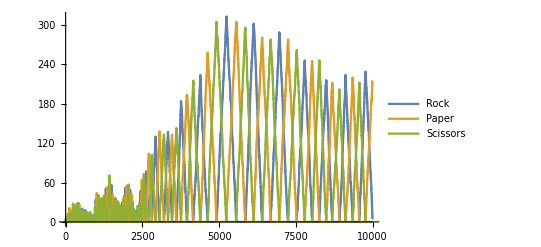

```mathematica
(* reprocess the history, assuming exactly one of each polymer, such that we plot their lengths *)
ListLinePlot[{
history/.{m_,state_}:>{m,state/.{R[n_]+a_+b_:> n}},
history/.{m_,state_}:>{m,state/.{P[n_]+a_+b_:> n}},
history/.{m_,state_}:>{m,state/.{S[n_]+a_+b_:> n}}
},PlotLegends->{Rock,Paper,Scissors}]
```

Can we make the oscillation more reliable?  We need to make sure that each polymer grows to, and shrinks from, the same length.  To do so, we couple together the growing and shrinking, one monomer for one monomer.  When shrinking, the polymer releases a monomer that can then attach to the “downstream” polymer.  In this case, we need to start with the desired total polymer length, rather than starting at zero and letting the fluctuations create the polymer.

The oscillation reliability problem is solved.  But a new problem becomes worth considering:  does the oscillator still work in bulk when there are multiple copies of each polymer type?  Apparently, no, this scheme does not work particularly well in that case... perhaps one could say that it simply doesn’t work.

```mathematica
ConstrainedPolymerRockPaperScissors={
rxnschema[R[0]+P[n_?(#>0&)],R[0]+P[n-1]+S,1],
rxnschema[S+S[n_],S[n+1],1],
rxnschema[P[0]+S[n_?(#>0&)],P[0]+S[n-1]+R,1],
rxnschema[R+R[n_],R[n+1],1],
rxnschema[S[0]+R[n_?(#>0&)],S[0]+R[n-1]+P,1],
rxnschema[P+P[n_],P[n+1],1]
};
```

```mathematica
Timing[history=SimulateReactionSchema[ConstrainedPolymerRockPaperScissors,R[100]+P[0]+S[0],10000]; Length[history]]
```

{49.0057,19848}

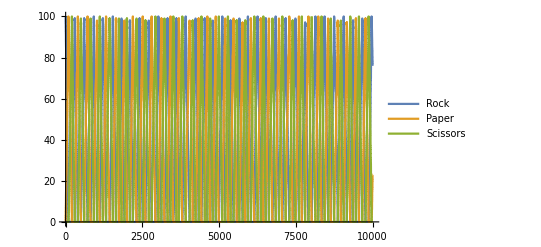

```mathematica
ListLinePlot[{
history/.{m_,state_}:>{m,state/.{R[n_]+a_+b_:> n}},
history/.{m_,state_}:>{m,state/.{P[n_]+a_+b_:> n}},
history/.{m_,state_}:>{m,state/.{S[n_]+a_+b_:> n}}
},PlotLegends->{Rock,Paper,Scissors}]
```

```mathematica
Timing[history=SimulateReactionSchema[ConstrainedPolymerRockPaperScissors,5R[100]+5P[0]+5S[0],1000]; Length[history]]
```

{38.8339,11993}

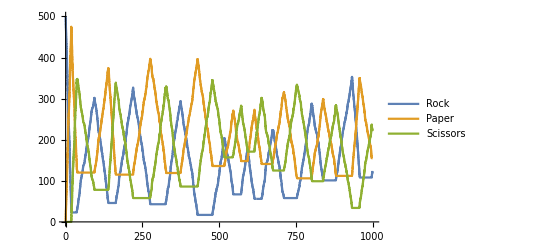

```mathematica
ListLinePlot[{
history/.{m_,state_}:>{m,state//.{R[n_]:> n, P[n_]:>0,S[n_]:>0,R->1,P->0,S->0}},
history/.{m_,state_}:>{m,state//.{R[n_]:> 0, P[n_]:>n,S[n_]:>0,R->0,P->1,S->0}},
history/.{m_,state_}:>{m,state//.{R[n_]:> 0, P[n_]:>0,S[n_]:>n,R->0,P->0,S->1}}
},PlotLegends->{Rock,Paper,Scissors}]
```

Our final construction can tolerate a least some extra copies... I am not sure how many, nor whether it would really work in bulk, in the limit.  It seems to get faster and less regular with slight increases in copy number.

How does it work? The problem with the previous scheme is that as soon as one of many copies of a polymer type, say R, reaches length zero, it will trigger the growth of the next polymer type, and the other copies of R will stop shrinking.  Thus, the total polymer length of a given type that must grow or shrink per cycle will not be constant.  What we would like is to make sure that R shrinks all the way for all copies, in each cycle.  We do that by making the first R stub also shrink R, not just P -- with both producing and growing S.  And so on.  So the first six reaction schemata are identical, and three more schemata are added.

```mathematica
SustainedPolymerRockPaperScissors={
rxnschema[R[0]+P[n_?(#>0&)],R[0]+P[n-1]+S,1],
rxnschema[S+S[n_],S[n+1],1],
rxnschema[P[0]+S[n_?(#>0&)],P[0]+S[n-1]+R,1],
rxnschema[R+R[n_],R[n+1],1],
rxnschema[S[0]+R[n_?(#>0&)],S[0]+R[n-1]+P,1],
rxnschema[P+P[n_],P[n+1],1],
rxnschema[R[0]+R[n_?(#>0&)],R[0]+R[n-1]+S,1],
rxnschema[P[0]+P[n_?(#>0&)],P[0]+P[n-1]+R,1],
rxnschema[S[0]+S[n_?(#>0&)],S[0]+S[n-1]+P,1]
};
```

```mathematica
Timing[history=SimulateReactionSchema[SustainedPolymerRockPaperScissors,R[100]+P[0]+S[0],1000]; Length[history]]
```

{2.21344,1960}

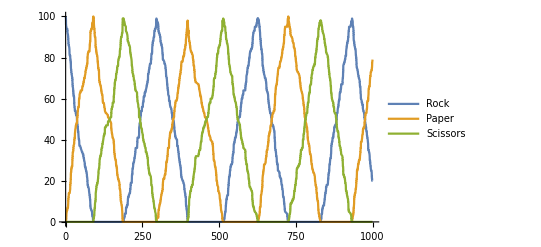

```mathematica
ListLinePlot[{
history/.{m_,state_}:>{m,state/.{R[n_]+a_+b_:> n}},
history/.{m_,state_}:>{m,state/.{P[n_]+a_+b_:> n}},
history/.{m_,state_}:>{m,state/.{S[n_]+a_+b_:> n}}
},PlotLegends->{Rock,Paper,Scissors}]
```

```mathematica
Timing[history=SimulateReactionSchema[SustainedPolymerRockPaperScissors,5R[100]+5P[0]+5S[0],1000]; Length[history]]
```

{549.457,42233}

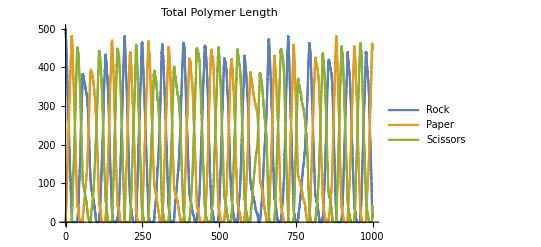

```mathematica
ListLinePlot[{
history/.{m_,state_}:>{m,state//.{R[n_]:> n, P[n_]:>0,S[n_]:>0,R->1,P->0,S->0}},
history/.{m_,state_}:>{m,state//.{R[n_]:> 0, P[n_]:>n,S[n_]:>0,R->0,P->1,S->0}},
history/.{m_,state_}:>{m,state//.{R[n_]:> 0, P[n_]:>0,S[n_]:>n,R->0,P->0,S->1}}
},PlotLegends->{Rock,Paper,Scissors},PlotLabel->"Total Polymer Length"]
```

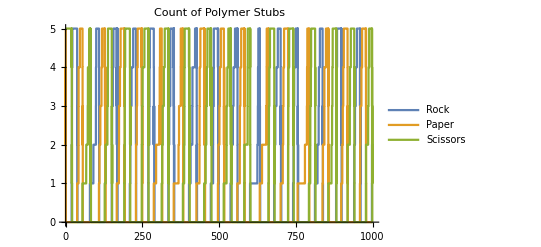

```mathematica
(* here we are looking at the copy number of the stubs, to see if they all get converted in each cycle *)
ListLinePlot[{
history/.{m_,state_}:>{m,state/.{R[0]->1,_Symbol[n_]->0,x:R|P|S->0}},
history/.{m_,state_}:>{m,state/.{P[0]->1,_Symbol[n_]->0,x:R|P|S->0}},
history/.{m_,state_}:>{m,state/.{S[0]->1,_Symbol[n_]->0,x:R|P|S->0}}
},PlotLegends->{Rock,Paper,Scissors},PlotLabel->"Count of Polymer Stubs"]
```

Although this is quite a good oscillator -- we expect O(√N) fluctuations in period O(N)  -- but that doesn’t definitively say anything about the intrinsic capabilities of PRNs vs CRNs for this task.  If you want to do that comparison, one might measure by (a) how many monomers are required, i.e. the volume, and (b) how many reaction mechanisms are required.  The schemes here use a constant number of reaction schemata to achieve arbitrary N, but the polymer length is effectively counting in unary, so the volume is O(N) . We could do better: an exercise to the reader would be to use a polymer binary counter to time the reactions, thereby getting O(√N) fluctuations with just O(log N) volume and still O(1) reaction schemata.  However, polymers are not necessary for efficiently counting in binary.  A CRN of size O(log N) can do it too, in volume O(log N).

An example is given below, again just for fun.  It would be interesting to make a solid comparison to CRN oscillators in the literature, as biochemical oscillators are well-studied in the biological and chemical traditions.

b[k,0] represents the k^th bit having value 0.  c[k] indicates a carry bit for the k^th position. The oscillating species can be taken to be b[K-1,1].  We could add two reactions such that b[K-1,1] produces X and b[K-1,0] degrades X a touch faster, yielding a more recognizable sawtooth -- but that would defeat the purpose of using a small volume, as it would be essentially a unary signal.

```mathematica
K=8; (* number of bits in counter; N = 2^K *)
BinaryCounterOscillatorCRN=Flatten[{
Table[rxninstance[c[k]+b[k,0],b[k,1]+c[0],1],{k,0,K-1}],
Table[rxninstance[c[k]+b[k,1],b[k,0]+c[Mod[k+1,K]],1],{k,0,K-1}]
}];
initialstate=c[0]+Sum[b[k,0],{k,0,K-1}];
```

```mathematica
BinaryCounterOscillatorCRN//MatrixForm
```

(rxninstance[b[0,0]+c[0],b[0,1]+c[0],1]
rxninstance[b[1,0]+c[1],b[1,1]+c[0],1]
rxninstance[b[2,0]+c[2],b[2,1]+c[0],1]
rxninstance[b[3,0]+c[3],b[3,1]+c[0],1]
rxninstance[b[4,0]+c[4],b[4,1]+c[0],1]
rxninstance[b[5,0]+c[5],b[5,1]+c[0],1]
rxninstance[b[6,0]+c[6],b[6,1]+c[0],1]
rxninstance[b[7,0]+c[7],b[7,1]+c[0],1]
rxninstance[b[0,1]+c[0],b[0,0]+c[1],1]
rxninstance[b[1,1]+c[1],b[1,0]+c[2],1]
rxninstance[b[2,1]+c[2],b[2,0]+c[3],1]
rxninstance[b[3,1]+c[3],b[3,0]+c[4],1]
rxninstance[b[4,1]+c[4],b[4,0]+c[5],1]
rxninstance[b[5,1]+c[5],b[5,0]+c[6],1]
rxninstance[b[6,1]+c[6],b[6,0]+c[7],1]
rxninstance[b[7,1]+c[7],b[7,0]+c[0],1])

```mathematica
(* this would be a lot faster if we used Soloveichik's CRNSimulatorSSA! *)
Timing[history=SimulateReactionSchema[BinaryCounterOscillatorCRN,initialstate,10000];]
```

{23.545,Null}

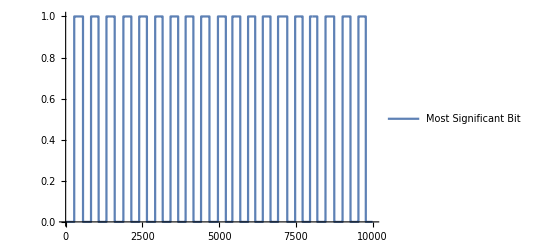

```mathematica
ListLinePlot[{DataTrace[history,b[K-1,1]]},PlotLegends->{"Most Significant Bit"}]
```

## A more “realistic” model: DNA and restriction enzymes

Our model of DNA will not allow fraying, bubbles, bulges, mismatches, or more secondary structure; but it will allow perfect duplex with nicks and gaps and overhangs.  A considerable subtlety in this example is that the representation of a DNA molecule can change if you “flip” it, and reactions should be independent of representation.  Another subtlety concerns interaction with Mathematica’s evaluation mechanisms: when using functions in the schemata, we need to be sure that they do not evaluate when their arguments are still pattern-matching variables, and thus that they only evaluate when those pattern-matching variables have been instantiated with valid content that represents a molecular component.   This is accomplished by setting the attribute HoldAll for rxnschema[ ], so that any function calls that may be present in the right-hand side (products) or in the rate formula will not be executed until those expressions are extracted and applied in a specific case.  Also demonstrated is that some functions and some patterns make use of the “ /; ” notation that indicates a pattern that should only be matched if the specified condition holds (e.g. that one sequence is the Watson-Crick complement of another sequence, or is of an appropriate length).  Also demonstrated here is a Format[ ] definition that makes Mathematica display molecular species in a more human-readable form... but only if the expression represents a fully specified molecule rather than a pattern to be matched.

The purpose of this section is just to gain an appreciation of how tricky it can be to formalize the action of real enzymes.  However, you are advised to skip it unless you are intrigued.

Calculating the Watson-Crick complement of a sequence will be a handy operation.

```mathematica
Clear[WC]
WC[A]=T; WC[T]=A; WC[C]=G; WC[G]=C;
WC[{seq___}]:=Reverse[{seq}/.{A->T,C->G,T->A,G->C}] 
WC[seq___]:=Sequence@@Reverse[{seq}/.{A->T,C->G,T->A,G->C}]
```

DNA molecules will be represented as expressions DNA[segment1,segment2,...] where each segment is either top[sequence], bot[sequence], or duplex[sequence], indicating single-stranded and double-stranded portions of the molecule.  A nick on the top strand would be represented as a bot[ ] segment, i.e. the bottom strand is connected by a zero-length single-stranded connector on the bottom.  Analogously for a nick on the bottom strand.  The definitions below ensure that segments are automatically combined where they can be combined.  To allow reactions between molecules in any orientation, we need to be able to flip the orientation.  For storing states, however, we only want to store a well-defined canonical orientation for each molecule.

```mathematica
Clear[DNA]
DNA[a___,duplex[s1__],duplex[s2__],b___]:=DNA[a,duplex[s1,s2],b]
DNA[a___,top[s1___],top[s2___],b___]:=DNA[a,top[s1,s2],b]
DNA[a___,bot[s1___],bot[s2___],b___]:=DNA[a,bot[s1,s2],b]
DNA[(top|bot)[],b___]:=DNA[b]
DNA[a___,(top|bot)[]]:=DNA[a]
Flip[duplex[s__]]:=duplex[WC[s]]
Flip[top[s___]]:=bot[WC[s]]
Flip[bot[s___]]:=top[WC[s]]
Flip[{d___}]:=Flip/@Reverse[{d}]
CanonicalDNA[DNA[d___]]:=If[OrderedQ[{Flip[{d}],{d}}] ,DNA@@Flip[{d}],DNA[d]]
```

Because the symbolic representation is a bit cumbersome to read, it’s nice to print out DNA molecules so that we can see the top and bottom strands easily.

```mathematica
Clear[TopStrand]
TopStrand[DNA[a___]]:=TopStrand[a]
TopStrand[]:={}
TopStrand[top[t__],s___]:=Join[{t},TopStrand[s]]
TopStrand[duplex[d__],s___]:=Join[{d},TopStrand[s]]
TopStrand[bot[],s___]:=Join[{" "},TopStrand[s]]
TopStrand[top[],s___]:=Join[{"-"},TopStrand[s]]
TopStrand[bot[t__],s___]:=Join[Table[" ",Length[{t}]],TopStrand[s]]
Clear[BotStrand]
BotStrand[DNA[a___]]:=BotStrand[a]
BotStrand[]:={}
BotStrand[bot[t__],s___]:=Join[WC/@{t},BotStrand[s]]
BotStrand[duplex[d__],s___]:=Join[WC/@{d},BotStrand[s]]
BotStrand[bot[],s___]:=Join[{"-"},BotStrand[s]]
BotStrand[top[],s___]:=Join[{" "},BotStrand[s]]
BotStrand[top[t__],s___]:=Join[Table[" ",Length[{t}]],BotStrand[s]]
```

```mathematica
Clear[SpecifiedQ]
SpecifiedQ[DNA[a:(_top|_bot|_duplex),b___]]:=SubsetQ[{A,C,T,G},List@@a]&&SpecifiedQ[DNA[b]]
SpecifiedQ[DNA[]]:=True
SpecifiedQ[DNA[__]]:=False
Format[DNA[s___]]:=MatrixForm[{TopStrand[DNA[s]],BotStrand[DNA[s]]}]/;SpecifiedQ[DNA[s]]
```

Let us look at a few examples of DNA molecules.

```mathematica
dna1=DNA[top[A,A,C],duplex[C,G,T,A,A,A],bot[T,G,T]]
```

(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)

```mathematica
dna1//FullForm
```

DNA[top[A,A,C],duplex[C,G,T,A,A,A],bot[T,G,T]]

```mathematica
CanonicalDNA[dna1]
```

(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)

```mathematica
dna2=DNA[duplex[A,C,C,C,T,G,A]]
```

(A | C | C | C | T | G | A
T | G | G | G | A | C | T)

```mathematica
CanonicalDNA[dna2]
```

(A | C | C | C | T | G | A
T | G | G | G | A | C | T)

```mathematica
dna3=DNA[top[A,C,C,A],duplex[C,G,G,G,A,G,T],bot[],duplex[G,A,G,A,T,T],bot[C,C,C]]
```

(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)

```mathematica
CanonicalDNA[dna3]
```

(G | G | G | A | A | T | C | T | C | - | A | C | T | C | C | C | G |   |   |   |  
  |   |   | T | T | A | G | A | G |   | T | G | A | G | G | G | C | A | C | C | A)

```mathematica
dna4=DNA[top[A,A,T,T,G],duplex[A,G,T,G,A,A,T,T,C,G,C,T,A,G,A,A,T,T,C,A,C,G],top[G,G,G]]
```

(A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
  |   |   |   |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  )

```mathematica
CanonicalDNA[dna4]
```

(  |   |   | C | G | T | G | A | A | T | T | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A)

Now that we have the DNA molecule format represented, we define rules that allow molecules to fall apart if they are connected only by “short” double-helical portions, to stick to each other (perhaps briefly) if they have a complementary region of any length, and of course to be cleaved by a restriction enzyme.  To test your abilities, consider how to write a reaction schema for ligation.

```mathematica
(* shorthand useful when defining rules, so that the products of a reaction are always in their canonical form *)
cDNA[x___]:=CanonicalDNA[DNA[x]]
```

```mathematica
Clear[DissocRate]
DissocRate[seq__]:=10^(6-Length[{seq}]) / 10^9  (* /nM/s *)
DissocLength = 10;
DissociationReactionSchemata = {
rxnschema[DNA[duplex[x__]]/;Length[{x}]<DissocLength, cDNA[bot[x]]+cDNA[top[x]],DissocRate[x]],
rxnschema[DNA[a___,b_bot,duplex[x__]]/;Length[{x}]<DissocLength,cDNA[a,b,bot[x]]+cDNA[top[x]],DissocRate[x]],
rxnschema[DNA[a___,b_top,duplex[x__]]/;Length[{x}]<DissocLength,cDNA[a,b,top[x]]+cDNA[bot[x]],DissocRate[x]],
rxnschema[DNA[duplex[x__],c_bot,d___]/;Length[{x}]<DissocLength,cDNA[bot[x],c,d]+cDNA[top[x]],DissocRate[x]],
rxnschema[DNA[duplex[x__],c_top,d___]/;Length[{x}]<DissocLength,cDNA[top[x],c,d]+cDNA[bot[x]],DissocRate[x]],
rxnschema[DNA[a___,b_bot,duplex[x__],c_top,d___]/;Length[{x}]<DissocLength,cDNA[a,b,bot[x]]+cDNA[top[x],c,d],DissocRate[x]],
rxnschema[DNA[a___,b_top,duplex[x__],c_bot,d___]/;Length[{x}]<DissocLength,cDNA[a,b,top[x]]+cDNA[bot[x],c,d],DissocRate[x]],
rxnschema[DNA[a___,b_bot,duplex[x__],c_bot,d___]/;Length[{x}]<DissocLength,cDNA[a,b,bot[x],c,d]+cDNA[top[x]],DissocRate[x]],
rxnschema[DNA[a___,b_top,duplex[x__],c_top,d___]/;Length[{x}]<DissocLength,cDNA[a,b,top[x],c,d]+cDNA[bot[x]],DissocRate[x]]
};
```

```mathematica
Clear[AssocRate]
AssocRate[seq__]:=10^-3   (* /nM/s *)
AssociationReactionSchemata = {
rxnschema[DNA[a___,top[b___,c__,d___],e___]+DNA[bot[c__]], cDNA[a,top[b],duplex[c],top[d],e],AssocRate[c]],
rxnschema[DNA[a___,bot[b___,c__,d___],e___]+DNA[top[c__]], cDNA[a,bot[b],duplex[c],bot[d],e],AssocRate[c]],
rxnschema[DNA[a___,top[b___,c__,d___],e___]+DNA[top[cc__]]/;{c}===WC[{cc}], cDNA[a,top[b],duplex[c],top[d],e],AssocRate[c]],
rxnschema[DNA[a___,bot[b___,c__,d___],e___]+DNA[bot[cc__]]/;{c}===WC[{cc}], cDNA[a,bot[b],duplex[c],bot[d],e],AssocRate[c]],
rxnschema[DNA[a___,top[b___,c__]]+DNA[bot[c__,d___],e___], cDNA[a,top[b],duplex[c],bot[d],e],AssocRate[c]],
rxnschema[DNA[a___,bot[b___,c__]]+DNA[top[c__,d___],e___], cDNA[a,bot[b],duplex[c],top[d],e],AssocRate[c]],
rxnschema[DNA[a___,top[b___,c__]]+DNA[e___,top[d___,cc__]]/;{c}===WC[{cc}], cDNA[a,top[b],duplex[c],bot[WC[d]],Sequence@@Flip[{e}]],AssocRate[c]],
rxnschema[DNA[a___,bot[b___,c__]]+DNA[e___,bot[d___,cc__]]/;{c}===WC[{cc}], cDNA[a,bot[b],duplex[c],top[WC[d]],Sequence@@Flip[{e}]],AssocRate[c]]
};
```

```mathematica
RestrictionRate=10^-3; (* /nM/s *)
RestrictionEnzymeReactionSchemata = {
 (* note that because the recognition sites for both these enzymes are symmetric, they will apply fine if the input DNA is always in canonical form, as typically will be the case *)
rxnschema[EcoRI + DNA[a___,duplex[b__,G,A,A,T,T,C,c__],d___],
EcoRI + cDNA[a,duplex[b,G],bot[A,A,T,T]]+cDNA[top[A,A,T,T],duplex[C,c],d], RestrictionRate],
rxnschema[SmlI + DNA[a___,duplex[b__,C,T,x:C|T,y:A|G,A,G,c__],d___], SmlI+cDNA[a,duplex[b,C],bot[T,x,y,A]]+cDNA[top[T,x,y,A],duplex[G,b],d],RestrictionRate]
};
```

Here, we just test whether the reaction schemata are being applied correctly to find all possible concrete reactions for a given pair of reactants or a given single reactant.

```mathematica
JITReactions[RestrictionEnzymeReactionSchemata[[1]],EcoRI,dna4]
```

{rxninstance[EcoRI+(A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
  |   |   |   |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  ),EcoRI+(  |   |   | C | G | T | G | A | A | T | T | C | T | A | G | C | G |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A | G | A | T | C | G | C | T | T | A | A)+(A | A | T | T | C | A | C | T |   |   |   |   |  
  |   |   |   | G | T | G | A | G | T | T | A | A),1/1000],rxninstance[EcoRI+(A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
  |   |   |   |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  ),EcoRI+(  |   |   | C | G | T | G |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A)+(A | A | T | T | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
  |   |   |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A),1/1000]}

```mathematica
JITReactions[DissociationReactionSchemata,dna3]
```

{rxninstance[(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),(  |   |   |   |   |   |   |   |   |   |  
T | G | A | G | G | G | C | A | C | C | A)+(  |   |   |   |   |   |   | G | A | G | A | T | T |   |   |  
G | C | C | C | T | C | A | C | T | C | T | A | A | G | G | G),1/10000000000],rxninstance[(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),(  |   |   |   |   |  
T | T | A | G | A | G)+(A | C | C | A | C | G | G | G | A | G | T |   |   |   |   |   |   |   |   |  
  |   |   |   | G | C | C | C | T | C | A | C | T | C | T | A | A | G | G | G),1/1000000000]}

```mathematica
JITReactions[AssociationReactionSchemata,dna3,DNA[bot[A,C,C,A]]]
```

{rxninstance[(  |   |   |  
T | G | G | T)+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),(A | C | C | A | - | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
T | G | G | T |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),1/1000],rxninstance[(  |   |   |  
T | G | G | T)+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),(A | C | C | A | - | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
T | G | G | T |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),1/1000],rxninstance[(  |   |   |  
T | G | G | T)+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),(  |   |   | A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
T | G | G | T |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),1/1000]}

```mathematica
JITReactions[AssociationReactionSchemata,dna3,DNA[top[C,C,C,C,A,T,G,G,T]]]
```

{rxninstance[(C | C | C | C | A | T | G | G | T
  |   |   |   |   |   |   |   |  )+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),(  |   |   |   |   |   | G | G | G | - | A | A | T | C | T | C | - | A | C | T | C | C | C | G |   |   |   |  
T | G | G | T | A | C | C | C | C |   | T | T | A | G | A | G |   | T | G | A | G | G | G | C | A | C | C | A),1/1000],rxninstance[(C | C | C | C | A | T | G | G | T
  |   |   |   |   |   |   |   |  )+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),(  |   |   |   |   |   |   | G | G | G | A | A | T | C | T | C | - | A | C | T | C | C | C | G |   |   |   |  
T | G | G | T | A | C | C | C | C |   | T | T | A | G | A | G |   | T | G | A | G | G | G | C | A | C | C | A),1/1000],rxninstance[(C | C | C | C | A | T | G | G | T
  |   |   |   |   |   |   |   |  )+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G),(  |   |   |   |   |   |   |   | G | G | G | A | A | T | C | T | C | - | A | C | T | C | C | C | G |   |   |   |  
T | G | G | T | A | C | C | C | C |   |   | T | T | A | G | A | G |   | T | G | A | G | G | G | C | A | C | C | A),1/1000]}

```mathematica
DetailedREschemata=Join[AssociationReactionSchemata,DissociationReactionSchemata,RestrictionEnzymeReactionSchemata];
```

```mathematica
history=SimulateReactionSchema[DetailedREschemata,EcoRI+dna1+dna2+dna3+3dna4,1000];
```

```mathematica
history
```

{{0,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+3 (A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
  |   |   |   |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  )+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)},{102.012,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+(  |   |   | C | G | T | G |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+(A | A | T | T | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
  |   |   |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A)+2 (A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
  |   |   |   |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  )+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)},{128.863,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+(A | A | T | T | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
  |   |   |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A)+(A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
  |   |   |   |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  )+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)+(  |   |   | C | G | T | G |   | A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
G | G | G | G | C | A | C | - | T | T | A | A |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  )},{294.555,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+(  |   |   | C | G | T | G | A | A | T | T | C | T | A | G | C | G |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A | G | A | T | C | G | C | T | T | A | A)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+(A | A | T | T | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
  |   |   |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A)+(A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
  |   |   |   |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  )+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)+(  |   |   | C | G | T | G |   | A | A | T | T | G | A | G | T | G |   |   |   |  
G | G | G | G | C | A | C | - | T | T | A | A |   | T | C | A | C | T | T | A | A)},{330.589,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+(  |   |   | C | G | T | G | A | A | T | T | C | T | A | G | C | G |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A | G | A | T | C | G | C | T | T | A | A)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+(A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
  |   |   |   |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  )+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)+(  |   |   | C | G | T | G |   | A | A | T | T | G | A | G | T | G |   | A | A | T | T | - | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
G | G | G | G | C | A | C | - | T | T | A | A |   | T | C | A | C | - | T | T | A | A |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A)},{376.666,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+(  |   |   | C | G | T | G |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+(A | A | T | T | C | G | C | T | A | G |   |   |   |  
  |   |   |   | G | C | G | A | T | C | T | T | A | A)+(A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G | A | A | T | T | C | A | C | G | G | G | G
  |   |   |   |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A | G | T | G | C |   |   |  )+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)+(  |   |   | C | G | T | G |   | A | A | T | T | G | A | G | T | G |   | A | A | T | T | - | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
G | G | G | G | C | A | C | - | T | T | A | A |   | T | C | A | C | - | T | T | A | A |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A)},{412.257,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+(  |   |   | C | G | T | G |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)+(  |   |   | C | G | T | G | A | A | T | T | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   | A | A | T | T | - | C | T | A | G | C | G |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A |   | G | A | T | C | G | C | T | T | A | A)+(  |   |   | C | G | T | G |   | A | A | T | T | G | A | G | T | G |   | A | A | T | T | - | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
G | G | G | G | C | A | C | - | T | T | A | A |   | T | C | A | C | - | T | T | A | A |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A)},{517.356,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+2 (  |   |   | C | G | T | G |   |   |   |  
G | G | G | G | C | A | C | T | T | A | A)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)+(A | A | T | T | C | G | C | T | A | G |   | A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G |   |   |   |  
  |   |   |   | G | C | G | A | T | C | - | T | T | A | A |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A)+(  |   |   | C | G | T | G |   | A | A | T | T | G | A | G | T | G |   | A | A | T | T | - | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
G | G | G | G | C | A | C | - | T | T | A | A |   | T | C | A | C | - | T | T | A | A |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A)},{626.851,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)+(  |   |   | C | G | T | G |   | A | A | T | T | - | C | A | C | G | G | G | G
G | G | G | G | C | A | C | - | T | T | A | A |   | G | T | G | C |   |   |  )+(A | A | T | T | C | G | C | T | A | G |   | A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G |   |   |   |  
  |   |   |   | G | C | G | A | T | C | - | T | T | A | A |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A)+(  |   |   | C | G | T | G |   | A | A | T | T | G | A | G | T | G |   | A | A | T | T | - | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   |   |   |   |  
G | G | G | G | C | A | C | - | T | T | A | A |   | T | C | A | C | - | T | T | A | A |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A)},{1020.2,EcoRI+(A | C | C | C | T | G | A
T | G | G | G | A | C | T)+(A | A | C | C | G | T | A | A | A |   |   |  
  |   |   | G | C | A | T | T | T | A | C | A)+(A | C | C | A | C | G | G | G | A | G | T |   | G | A | G | A | T | T |   |   |  
  |   |   |   | G | C | C | C | T | C | A | - | C | T | C | T | A | A | G | G | G)+(  |   |   | C | G | T | G |   | A | A | T | T | - | C | A | C | G | G | G | G
G | G | G | G | C | A | C | - | T | T | A | A |   | G | T | G | C |   |   |  )+(  |   |   | C | G | T | G |   | A | A | T | T | G | A | G | T | G |   | A | A | T | T | - | C | T | A | G | C | G | A | A | T | T | C | A | C | T |   | A | A | T | T | - | C | G | C | T | A | G |   | A | A | T | T | G | A | G | T | G | A | A | T | T | C | G | C | T | A | G |   |   |   |  
G | G | G | G | C | A | C | - | T | T | A | A |   | T | C | A | C | - | T | T | A | A |   | G | A | T | C | G | C | T | T | A | A | G | T | G | A | G | T | T | A | A |   | G | C | G | A | T | C | - | T | T | A | A |   | T | C | A | C | T | T | A | A | G | C | G | A | T | C | T | T | A | A)}}

## Class lecture example of restriction enzymes

In class we considered a simple set of 3 reaction schemata that crudely modeled the restriction enzyme EcoRI cutting DNA and the enzyme Ligase joining the pieces back together again, perhaps with a new partner.  Because our Reaction Schema Simulator does not handle trimolecular (or higher) reactions, we must decompose the ligation reaction into steps.   The two natural possibilities are: (a) first DNA strands hybridize by their sticky ends, then ligase comes along and glues them permanently, or (b) ligase finds a DNA molecule and hangs onto it until, together, the bump into another DNA with a matching sticky end, whereupon ligation occurs.   These are both plausible, and indeed both pathways are thought to occur; which one is more likely will depend on the concentration of DNA, the concentration of ligase, the length of the sticky end, and other factors.  For simplicity, let’s only model one, but which one?  For molecules in a bacterial-sized 1.66 fL volume, suppose all counts are 1.  The fastest enzymes (diffusion-limited ones) have rate constants on the order of 10^8 /M/s and act on small (i.e. fast-diffusing) substrates.  That’s 0.1 /nM/s.  So in this volume, 1 enzyme would require on average 10 seconds to find its single-copy substrate.  DNA hybridization for short sticky ends is about 10^7/M/s at room temperature, so 1 copy each in this volume will take 100 seconds to fine each other, but a 4-nucleotide sticky end will dissociate quickly, perhaps at a rate of 100 /s.  That is, the fraction of time that the molecules are stuck together is 10^-4 with these numbers. So our 1 molecule of ligase will require 10^5 seconds by this pathway.  Now the other pathway.  T4 DNA ligase has Michaelis-Menten parameters of roughly k_cat=1 /s and K_M=2 nM, so assuming the on-rate is 10^9 /M/s, the off rate must be 1 /s, which is comparable with k_cat and could be considered very slow for a molecular event.  In particular, it is sure to be slower than the dissociation of a 4-base sticky end, perhaps by a factor of 100.  So we’ll model pathway (b): ligase will arrive, hang out on a sticky end for a while, and if a matching strand comes by, zing!  Properly speaking, ligase could bind to either end of a DNA molecule, but since we represent the flipping of the molecule, we just implement a single reaction schema with the understanding that effectively our rate constant is different by a factor of 2 (since the molecule can reaction only half the time).  That’s no biggie.

EcoRI has rough Michaelis-Menten parameters for E+S ↔ ES → ES’ → E’+S with k_M= 10 nM, k_cat= 1 /s, and k_release = 0.01 /s  where the first reversible step is binding, the second step is cleavage, and the third step is release of the enzyme back into solution.  Of course there are more detailed models, but we don’t even want this level of complexity.  If we won’t use the model under saturating conditions (too much enzyme or too much substrate) then we can just go with a bimolecular reaction with rate constant 0.01 /nM/sec such that with a count of 1 in 1.66 fL, the release will be rate-limiting.

We use helper functions to describe the logic of “flipping” the representation of a molecule; these functions execute after substitution when building a reaction instance from the schema.  Also note that we play with fire and use the symbol C (used by coefficients in algebra) within our DNA objects.

```mathematica
Clear[DNA,flip,kLigaseAssoc,kLigaseDissoc,kRestrict,kAssocDNA,A,T,G,tA,tT,tC,tG,bA,bT,bC,bG,EcoRI,Ligase];
flip[seq___]:=Sequence@@Reverse[{seq}/.{A->T,T->A,C->G,G->C,bA->tA,bT->tT,bC->tC,bG->tG,tA->bA,tT->bT,tC->bC,tG->bG}]
kLigaseAssoc=1; (* /nM/s *)
kLigaseDissoc=1; (* /s *)
kRestrict=0.01; (* 10^7 /M/s in /nM/s units, since restriction enzymes are more complex *)
kAssocDNA = 0.1; (* 10^8 /M/s in /nM/s units, which is not unrealistic if the ligase helps stabilize the DNA, since 10^7 /M/s is typical for short oligonucleotides *)
kFlip=0.01; (* to avoid redundant flipping, no faster than the slowest reaction when there is just 1 molecule *)

EcoRIschemata={
rxnschema[EcoRI+DNA[left___,G,A,A,T,T,C,right___],EcoRI+DNA[left,G,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,C,right],kRestrict],
rxnschema[Ligase+DNA[left___,bT,bT,bA,bA],DNA[left,bT,bT,bA,bA,Ligase],kLigaseAssoc],
rxnschema[DNA[left___,bT,bT,bA,bA,Ligase],Ligase+DNA[left,bT,bT,bA,bA],kLigaseDissoc],
rxnschema[DNA[left___,bT,bT,bA,bA,Ligase]+DNA[tA,tA,tT,tT,right___],Ligase+DNA[left,A,A,T,T,right],kAssocDNA],
rxnschema[DNA[seq___],DNA[flip[seq]],kFlip]
};
```

```mathematica
dna1=DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,A,A,T,T,C,C,C,C,C,C,C,C,C];
```

```mathematica
(history=SimulateReactionSchema[EcoRIschemata,EcoRI+dna1,180])//MatrixForm
```

(0 | EcoRI+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,A,A,T,T,C,C,C,C,C,C,C,C,C]
15.7575 | EcoRI+DNA[G,G,G,G,G,G,G,G,G,A,A,T,T,C,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,A,T,T,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C]
44.0453 | EcoRI+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,C,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,A,T,T,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C]
59.1321 | EcoRI+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
195.03 | EcoRI+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA])

```mathematica
(history=SimulateReactionSchema[EcoRIschemata,Last[Last[history]]/.EcoRI->Ligase,180])//MatrixForm
```

(0 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
0.00160829 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,bT,bT,bA,bA,Ligase]+DNA[tA,tA,tT,tT,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
1.56426 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
1.68355 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
2.366 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
2.47898 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
2.96425 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
4.05536 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
4.25347 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
4.6211 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
5.49941 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
5.83375 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
6.45545 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
7.65419 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
8.49448 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
9.01141 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
10.899 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
11.0238 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
11.8017 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
12.2827 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
13.0159 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
13.3173 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
13.706 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
14.3076 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
14.819 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
14.9839 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
16.7057 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
16.9154 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
19.0829 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
19.3581 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
19.5392 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
20.0018 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
20.3182 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
20.4112 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
21.3863 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
21.7396 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
23.5984 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
23.6079 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
24.2288 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
25.3258 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
27.1101 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
27.4205 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
28.1459 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
28.2488 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
28.3198 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
31.0514 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
31.6504 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
32.7033 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
34.1974 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
35.2269 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
36.4899 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
36.9493 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
39.6488 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
40.0162 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
40.0783 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
41.3327 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
41.4199 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
41.5478 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
41.681 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
42.3047 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
45.2823 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
46.0601 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
48.0136 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
48.0231 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
53.4748 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
53.5392 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
54.0683 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
54.4969 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
55.0302 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
55.1024 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
56.4403 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
57.2064 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
57.2311 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
57.3935 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
57.7191 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
57.8652 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
58.488 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
59.6841 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
59.9203 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
59.9265 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
60.3672 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
60.3674 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
60.7402 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
60.8414 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
61.446 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
61.56 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
62.6546 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
62.7799 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
64.6174 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
65.6221 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
66.2135 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
67.6882 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
68.533 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
68.9542 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
70.2022 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
70.4899 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
71.7575 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
71.8521 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
75.1043 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
75.6286 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
75.6445 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
76.5813 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
78.1038 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
78.2148 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
78.337 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
78.3415 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
78.5066 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
79.4632 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
80.0997 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
80.6961 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
81.67 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
82.0658 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
83.1637 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
83.5575 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
83.579 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
84.4235 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
86.2745 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
87.9979 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
88.1782 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
88.7353 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
90.6722 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
91.7577 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
92.7346 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
94.535 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA,Ligase]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
94.6015 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
95.1577 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
95.2902 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
95.8041 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
96.424 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
96.6959 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
97.0966 | Ligase+DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
97.1091 | DNA[G,G,G,G,G,G,G,G,G,bT,bT,bA,bA]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
97.1592 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
98.1991 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
98.309 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
100.427 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
100.527 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
101.478 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
101.727 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
102.632 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
104.668 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
104.84 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
106.06 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
106.09 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
109.455 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
110.38 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
111.666 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
112.573 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
114.072 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
114.411 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
115.032 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
115.409 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
116.263 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
118.146 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
118.25 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
118.674 | Ligase+DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA]
119.21 | DNA[tA,tA,tT,tT,C,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,bT,bT,bA,bA,Ligase]
119.397 | Ligase+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,G,A,A,T,T,C,C,C,C,C,C,C,C,C]
346.947 | Ligase+DNA[G,G,G,G,G,G,G,G,G,A,A,T,T,C,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,A,T,T,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C])

With the assistance of a few more helper functions, we can generalize to ligation of arbitrary-length sticky ends, so that addition other restriction enzymes is straightforward.  Here we have added  MfeI and SalI, with different fixed recognition sequences; SmlI, AwlNI, and BglI, restriction enzymes with degenerate recognition sequences, and FokI, a type-IIS restriction enzyme that cuts a certain distance away from the recognition site.    Additional real restriction enzymes can be found at New England Biolabs ( https://enzymefinder.neb.com ) among other places.

We play one dirty trick in the final reaction schema for ligation:  if Ligase has attached itself to both sticky ends, we don’t let that prevent the ligation from occurring.   Inhibition due to saturation is a real thing in some molecular systems, but I don’t know whether it’s relevant for ligation (by T4 DNA Ligase or other ligases).  The motivation here is simply to prevent slow simulations that “waste” their time modeling Ligase attaching and detaching.   The simplest encoding as a Mathematica pattern, using “...” to represent a sequence of zero or more instances, allows for more than one Ligase on one of the sticky ends, but this case will never arise from an appropriate initial state.

```mathematica
Clear[flip,botstrand,topstrand,duplex,complement]; (* helper functions *)
Clear[rates,kLigaseAssoc,kLigaseDissoc,kRestrict,kAssocDNA,kFlip]; (* symbolic rate constants, and default parameter list *)
Clear[DNA,A,T,G,tA,tT,tC,tG,bA,bT,bC,bG,EcoRI,SmlI,FokI,Ligase]; (* symbols in species expressions *)
flip[seq___]:=Sequence@@Reverse[{seq}/.{A->T,T->A,C->G,G->C,bA->tA,bT->tT,bC->tC,bG->tG,tA->bA,tT->bT,tC->bC,tG->bG}]
botstrand[seq___]:=Sequence@@({seq}/.{A->bT,T->bA,C->bG,G->bC})
topstrand[seq___]:=Sequence@@({seq}/.{A->tA,T->tT,C->tC,G->tG})
duplex[seq___]:=Sequence@@({seq}/.{bA->T,bT->A,bC->G,bG->C,tA->A,tT->T,tC->C,tG->G})
complement[seq___]:=Sequence@@({seq}/.{bA->tT,bT->tA,bC->tG,bG->tC,tA->bT,tT->bA,tC->bG,tG->bC})
rates={
kLigaseAssoc->1, (* /nM/s *)
kLigaseDissoc->1, (* /s *)
kRestrict->0.01, (* 10^7 /M/s in /nM/s units, since restriction enzymes are more complex *)
kAssocDNA -> 0.1, (* 10^8 /M/s in /nM/s units, which is not unrealistic if the ligase helps stabilize the DNA, since 10^7 /M/s is typical for short oligonucleotides *)
kFlip->0.01 (* to avoid redundant flipping, no faster than the slowest reaction when there is just 1 molecule *)
};

REschemata={ 
(* restriction enzymes cut at recognition sites *)
rxnschema[EcoRI+DNA[left___,G,A,A,T,T,C,right___],EcoRI+DNA[left,G,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,C,right],kRestrict],
rxnschema[MfeI+DNA[left___,C,A,A,T,T,G,right___],MfeI+DNA[left,C,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,G,right],kRestrict],
rxnschema[SalI+DNA[left___,G,T,C,G,A,C,right___],SalI+DNA[left,G,bA,bG,bC,bT]+DNA[tT,tC,tG,tA,C,right],kRestrict],
rxnschema[SmlI+DNA[left___,C,T,x:C|T,y:A|G,A,G,right___],SmlI+DNA[left,C,botstrand[T,x,y,A]]+DNA[topstrand[T,x,y,A],G,right],kRestrict], 
rxnschema[AlwNI+DNA[left___,C,A,G,x_,y_,z_,C,T,G,right___],AlwNI+DNA[left,C,A,G,topstrand[x,y,z]]+DNA[botstrand[x,y,z],C,T,G,right],kRestrict], 
rxnschema[BglI+DNA[left___,G,C,C,a_,x_,y_,z_,b_,G,G,C,right___],BglI+DNA[left,G,C,C,a,topstrand[x,y,z]]+DNA[botstrand[x,y,z],b,G,G,C,right],kRestrict], 
rxnschema[FokI+DNA[left___,G,G,A,T,G,gap:(A|T|C|G)..,sticky:(A|T|C|G)..,right___]/;Length[{gap}]==9&&Length[{sticky}]==4,FokI+DNA[left,G,G,A,T,G,gap,botstrand[sticky]]+DNA[topstrand[sticky],right],kRestrict],

(* ligase doing its thing *)
rxnschema[Ligase+DNA[left___,end:(bA|bT|bC|bG|tA|tT|tC|tG)],DNA[left,end,Ligase],kLigaseAssoc],
rxnschema[DNA[seq___,Ligase],Ligase+DNA[seq],kLigaseDissoc],
rxnschema[DNA[left___,stack1:(A|T|C|G),sticky1:(bA|bT|bC|bG|tA|tT|tC|tG)..,Ligase]+DNA[extra:Ligase...,sticky2:(bA|bT|bC|bG|tA|tT|tC|tG)..,stack2:(A|T|C|G),right___]/;{sticky1}==={complement[sticky2]},
Ligase+DNA[left,stack1,duplex[sticky1],stack2,right]+extra,kAssocDNA],

(* flipping molecular orientation *)
rxnschema[DNA[seq___],DNA[flip[seq]],kFlip]
};
```

```mathematica
dna1=DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,C,A,A,T,T,G,C,C,C,C,C,C,C,C];
dna2=DNA[A,A,A,C,C,A,G,T,C,G,A,C,T,T,T,G,T,G,C,T,T,G,A,G,A,C,A,C,G];
dna3=DNA[A,T,C,A,G,C,T,C,C,T,G,A,A,G,A,G,G,C,C,T,T,G,A,A,G,G,C,A,C,C,C];
dna4=DNA[G,G,G,G,A,T,G,T,A,A,A,A,T,G,C,T,A,T,C,T,C,A,A,A];
```

```mathematica
ToDNA[s_String]:=DNA@@ToExpression/@Characters[s]
FromDNA[dna_DNA]:=StringJoin@@(ToString/@dna)
 (* example usage *)
ToDNA["TAATACGACTCACTATAGGG"] //FullForm
FromDNA[DNA[G,A,T,T,A,C,A]] //FullForm
```

DNA[T,A,A,T,A,C,G,A,C,T,C,A,C,T,A,T,A,G,G,G]

"GATTACA"

```mathematica
(history=SimulateReactionSchema[REschemata/.rates,EcoRI+MfeI+dna1,200])//MatrixForm
```

(0 | EcoRI+MfeI+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,C,A,A,T,T,G,C,C,C,C,C,C,C,C]
2.72434 | EcoRI+MfeI+DNA[G,G,G,G,G,G,G,G,C,A,A,T,T,G,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,A,T,T,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C]
47.6072 | EcoRI+MfeI+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,A,A,T,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,A,T,C,C,A,A,T,T,G,C,C,C,C,C,C,C,C]
138.199 | EcoRI+MfeI+DNA[G,G,G,G,G,G,G,G,C,A,A,T,T,G,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,A,T,T,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C]
139.981 | EcoRI+MfeI+DNA[G,G,G,G,G,G,G,G,C,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,G,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,A,T,T,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C]
177. | EcoRI+MfeI+DNA[G,G,G,G,G,G,G,G,C,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C]+DNA[tA,tA,tT,tT,G,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,bT,bT,bA,bA]
179.178 | EcoRI+MfeI+DNA[tA,tA,tT,tT,G,C,C,C,C,C,C,C,C]+DNA[tA,tA,tT,tT,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C]+DNA[tA,tA,tT,tT,G,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,bT,bT,bA,bA]
179.304 | EcoRI+MfeI+DNA[G,G,G,G,G,G,G,G,C,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C]+DNA[tA,tA,tT,tT,G,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,bT,bT,bA,bA]
192.33 | EcoRI+MfeI+DNA[tA,tA,tT,tT,G,C,C,C,C,C,C,C,C]+DNA[tA,tA,tT,tT,C,G,C,G,C,G,C,G,C,G,C,G,C,G,C]+DNA[tA,tA,tT,tT,G,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,bT,bT,bA,bA]
256.437 | EcoRI+MfeI+DNA[tA,tA,tT,tT,G,C,C,C,C,C,C,C,C]+DNA[G,C,G,C,G,C,G,C,G,C,G,C,G,C,G,bT,bT,bA,bA]+DNA[tA,tA,tT,tT,G,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,A,T,G,bT,bT,bA,bA])

```mathematica
(history=SimulateReactionSchema[REschemata/.rates,SalI+SmlI+dna2,200])//MatrixForm
```

(0 | SalI+SmlI+DNA[A,A,A,C,C,A,G,T,C,G,A,C,T,T,T,G,T,G,C,T,T,G,A,G,A,C,A,C,G]
67.0884 | SalI+SmlI+DNA[C,G,T,G,T,C,T,C,A,A,G,C,A,C,A,A,A,G,T,C,G,A,C,T,G,G,T,T,T]
141.16 | SalI+SmlI+DNA[tT,tC,tG,tA,C,T,G,G,T,T,T]+DNA[C,G,T,G,T,C,T,C,A,A,G,C,A,C,A,A,A,G,bA,bG,bC,bT]
143.477 | SalI+SmlI+DNA[A,A,A,C,C,A,G,bA,bG,bC,bT]+DNA[C,G,T,G,T,C,T,C,A,A,G,C,A,C,A,A,A,G,bA,bG,bC,bT]
229.553 | SalI+SmlI+DNA[C,G,T,G,T,C,bA,bG,bT,bT]+DNA[A,A,A,C,C,A,G,bA,bG,bC,bT]+DNA[tT,tC,tA,tA,G,C,A,C,A,A,A,G,bA,bG,bC,bT])

```mathematica
(history=SimulateReactionSchema[REschemata/.rates,AlwNI+BglI+dna3,200])//MatrixForm
```

(0 | AlwNI+BglI+DNA[A,T,C,A,G,C,T,C,C,T,G,A,A,G,A,G,G,C,C,T,T,G,A,A,G,G,C,A,C,C,C]
61.3562 | AlwNI+BglI+DNA[G,G,G,T,G,C,C,T,T,C,A,A,G,G,C,C,T,C,T,T,C,A,G,G,A,G,C,T,G,A,T]
130.067 | AlwNI+BglI+DNA[G,G,G,T,G,C,C,T,tT,tC,tA]+DNA[bA,bG,bT,A,G,G,C,C,T,C,T,T,C,A,G,G,A,G,C,T,G,A,T]
172.21 | AlwNI+BglI+DNA[G,G,G,T,G,C,C,T,tT,tC,tA]+DNA[A,T,C,A,G,C,T,C,C,T,G,A,A,G,A,G,G,C,C,T,tT,tG,tA]
188.878 | AlwNI+BglI+DNA[bA,bC,bT,A,G,G,C,A,C,C,C]+DNA[A,T,C,A,G,C,T,C,C,T,G,A,A,G,A,G,G,C,C,T,tT,tG,tA]
199.592 | AlwNI+BglI+DNA[A,T,C,A,G,tC,tT,tC]+DNA[bA,bC,bT,A,G,G,C,A,C,C,C]+DNA[bG,bA,bG,C,T,G,A,A,G,A,G,G,C,C,T,tT,tG,tA]
298.202 | AlwNI+BglI+DNA[bC,bT,bC,C,T,G,A,T]+DNA[bA,bC,bT,A,G,G,C,A,C,C,C]+DNA[bG,bA,bG,C,T,G,A,A,G,A,G,G,C,C,T,tT,tG,tA])

```mathematica
(history=SimulateReactionSchema[REschemata/.rates,FokI+dna4,200])//MatrixForm
```

(0 | FokI+DNA[G,G,G,G,A,T,G,T,A,A,A,A,T,G,C,T,A,T,C,T,C,A,A,A]
0.384651 | FokI+DNA[T,T,T,G,A,G,A,T,A,G,C,A,T,T,T,T,A,C,A,T,C,C,C,C]
244.428 | FokI+DNA[G,G,G,G,A,T,G,T,A,A,A,A,T,G,C,T,A,T,C,T,C,A,A,A])

```mathematica
(history=SimulateReactionSchema[REschemata/.rates,Last[Last[history]]/.EcoRI|MfeI|SalI|SmlI|AlwNI|BglI|FokI->Ligase,200])//MatrixForm
```

(0 | Ligase+DNA[G,G,G,G,A,T,G,T,A,A,A,A,T,G,C,T,A,T,C,T,C,A,A,A]
120.44 | Ligase+DNA[T,T,T,G,A,G,A,T,A,G,C,A,T,T,T,T,A,C,A,T,C,C,C,C]
187.956 | Ligase+DNA[G,G,G,G,A,T,G,T,A,A,A,A,T,G,C,T,A,T,C,T,C,A,A,A]
290.51 | Ligase+DNA[T,T,T,G,A,G,A,T,A,G,C,A,T,T,T,T,A,C,A,T,C,C,C,C])

### Some relevant references

-- add Fontana ALIFE reference mentioned at the top, and some Soloveichik reference --  

Faeder, James R., Michael L. Blinov, and William S. Hlavacek. “Rule-based modeling of biochemical systems with BioNetGen.” In Systems biology, pp. 113-167. Humana Press, 2009.
Boutillier, Pierre, Mutaamba Maasha, Xing Li, Héctor F. Medina-Abarca, Jean Krivine, Jérôme Feret, Ioana Cristescu, Angus G. Forbes, and Walter Fontana. “The Kappa platform for rule-based modeling.” Bioinformatics 34, no. 13 (2018): i583-i592.
Johnson, Robert F., and Erik Winfree. “Verifying polymer reaction networks using bisimulation.” Theoretical Computer Science 843 (2020): 84-114.
Head, Tom. “Formal language theory and DNA: an analysis of the generative capacity of specific recombinant behaviors.” Bulletin of mathematical biology 49, no. 6 (1987): 737-759.